```mathematica
V100Timings=Import["/home/mathieut/Dropbox/ornl-determinism/reduction_results/V100/performance_results_.csv"];
GH200Timings=Import["/home/mathieut/Dropbox/ornl-determinism/reduction_results/GH200/performance_results_.csv"];
MI250XTimings=Import["/home/mathieut/Dropbox/ornl-determinism/reduction_results/Mi250X/performance_results_Mi250X.csv"];
LatexAbbrev[st_]:=Switch[st,"single_pass_gpu_shuffle","\\gls{SPS}","single_pass_gpu_shuffle_recursive","\\gls{SPSR}","single_pass_gpu_shuffle_kahan","\\gls{SPSK}","single_pass_gpu_shuffle_atomic","\\gls{SPSA}","two_pass_gnu_det_shuffle_kahan_cpu","\\gls{SPSKC}","two_pass_gnu_det_shuffle_recursive_cpu","\\gls{SPSRC}","single_pass_gpu_shared","\\gls{SPS}","single_pass_gpu_kahan","\\gls{SPK}","single_pass_det_recursive","\\gls{SPR}","single_pass_gpu_shared_atomic","\\gls{SPSA}","two_pass_gnu_det_recursive_cpu","\\gls{TPRC}","two_pass_gnu_det_kahan_cpu","\\gls{TPKC}","cub_reduce","\\gls{CU}","atomic_only","\\gls{AO}"];
ExtractMostPerf[GPU_,lst_,nm_]:=Map[{LatexAbbrev[#[[1]]],GPU<>" ("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")",Around[#[[4]],#[[5]]],100(1-#[[4]]/Min[MI250XTimings[[All,4]]])}&,lst[[Ordering[lst[[All,4]]][[1;;nm]]]]]
```

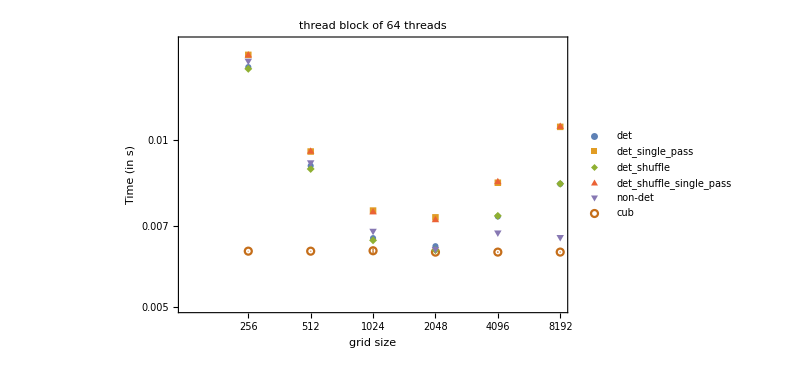
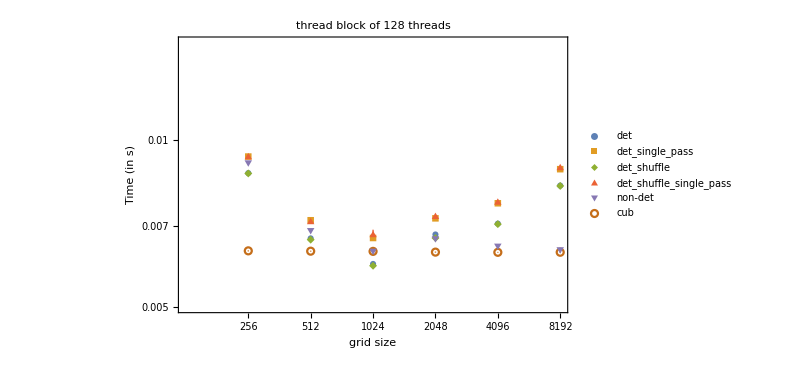
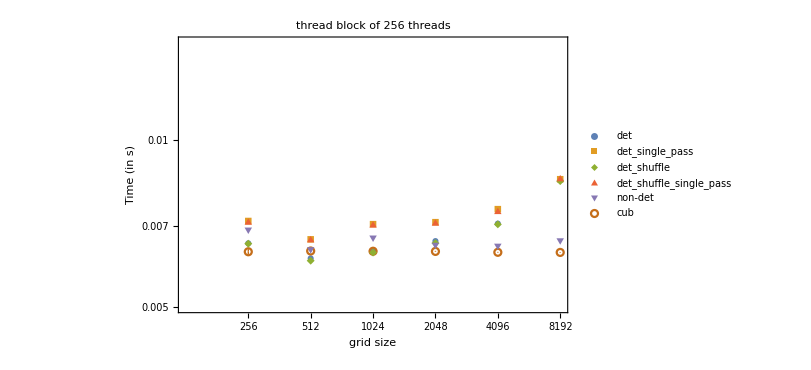
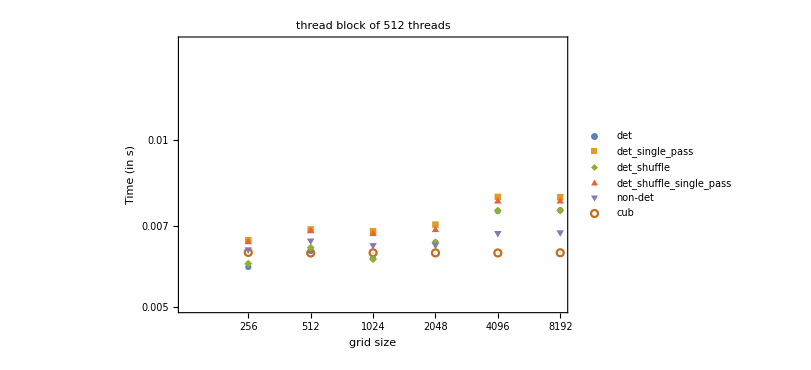
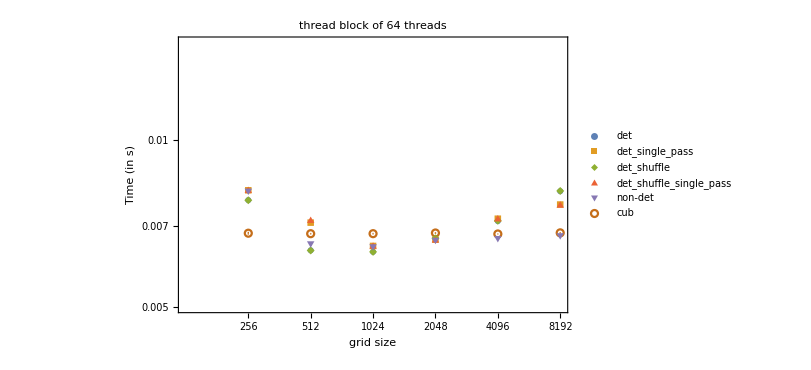
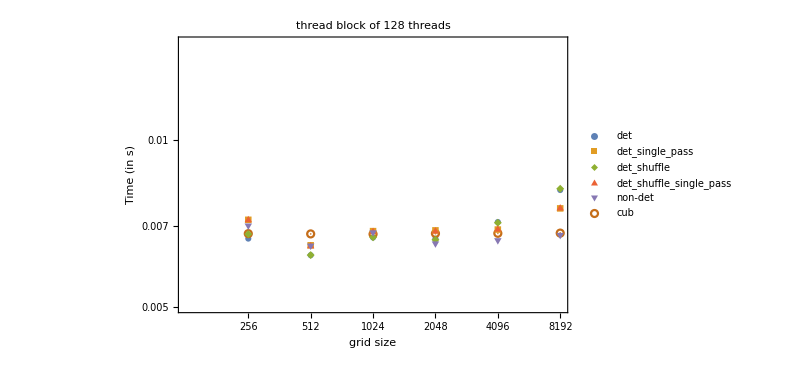
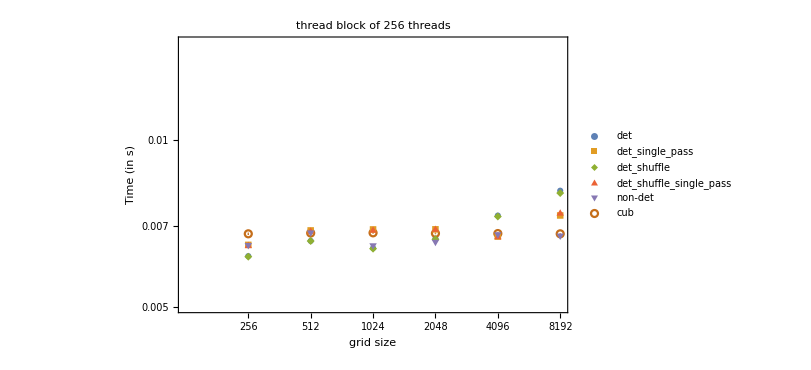
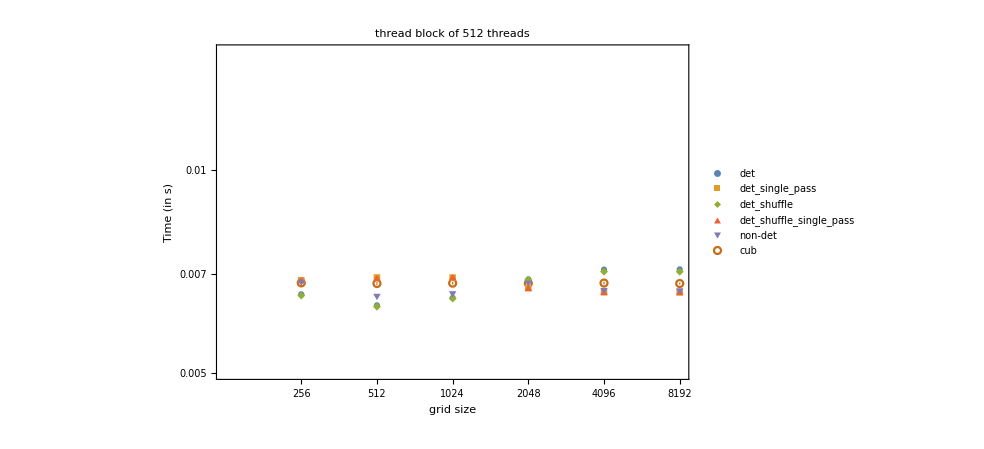

```mathematica
gs=Map[Table[ListLogPlot[Transpose[Table[Around[#[[im,i,j]],#[[im,i,j+1]]],{i,8,Length[#[[1]]]-2},{j,3,14,2}]],PlotLegends->Placed[Leg[[3;;8]],{Center,Top}],PlotTheme->"Detailed",PlotMarkers->Automatic, PlotRange->{Automatic, {0.005,0.015}},FrameTicks->{Automatic, {Table[{i-7,GridSize[[i]]},{i,8,14}],None}},FrameLabel->{"grid size","Time (in s)"},PlotLabel->"thread block of "<>ToString[blockSize[[im]]]<>" threads",ImageSize->600],{im,1,4}]&,{DataMi250,DataV100}]
```

```mathematica
..
```

```mathematica
Table[Export["timings_mi250x_"<>ToString[blockSize[[i]]]<>".pdf",gs[[1,i]]],{i,1,4}]
Table[Export["timings_V100_"<>ToString[blockSize[[i]]]<>".pdf",gs[[2,i]]],{i,1,4}]
```

{timings_mi250x_64.pdf,timings_mi250x_128.pdf,timings_mi250x_256.pdf,timings_mi250x_512.pdf}

{timings_V100_64.pdf,timings_V100_128.pdf,timings_V100_256.pdf,timings_V100_512.pdf}

```mathematica
Map[1-#/#[[6]]&,DataV100[[4,All,3;;14;;2]]]
```

{{-11.1576,-11.3373,-11.1797,-11.2305,-11.2144,0.},{-5.401,-5.51311,-5.4022,-5.46534,-5.45021,1.11022×10^-16},{-2.45245,-2.58833,-2.45957,-2.54215,-2.50272,1.11022×10^-16},{-0.947974,-0.99878,-0.946145,-0.999692,-0.99721,0.},{-0.175385,-0.312978,-0.191286,-0.305477,-0.232461,0.},{0.0535195,-0.0512939,0.0537492,-0.0545937,0.0108339,0.},{0.0959585,0.0423703,0.0990379,0.0435413,0.0505726,0.},{0.0381319,-0.0092643,0.0422007,-0.00993707,-0.000437278,0.},{0.071707,-0.0206188,0.0761425,-0.0187125,0.0450156,0.},{0.0487335,-0.0191828,0.0512043,-0.0210348,0.037776,0.},{-0.0136272,0.0164701,-0.0121902,0.0154626,0.0016765,0.},{-0.0471818,0.0311948,-0.0397471,0.0294777,0.0272961,0.},{-0.0495823,0.0302113,-0.0411693,0.0276255,0.0268433,0.},{-0.0483472,0.0311145,-0.0407077,0.0280693,0.0276802,0.},{-0.0489217,0.0306081,-0.040824,0.027446,0.027346,0.}}

```mathematica
V100Timings//Length
```

560

```mathematica
dd[[1,Position[dd[[1,All,4]],Min[dd[[1,All,4]]]][[1]]]]
```

{{single_pass_gpu_shuffle,256,256,0.00650785,8.39892×10^-6}}

```mathematica
dd[[1,All,4]]
```

{0.0229185,0.0127123,0.00817054,0.00731063,0.00666854,0.00677769,0.00753063,0.00782793,0.00876786,0.0119218,0.0126749,0.00874362,0.00722115,0.00664872,0.00700658,0.00710008,0.0070304,0.00769495,0.00801235,0.00798801,0.0083059,0.00716865,0.00650785,0.00703716,0.00707585,0.00708751,0.00688791,0.00741396,0.00742837,0.00744824,0.00716266,0.00651377,0.0069014,0.00709188,0.00706556,0.00685059,0.00679341,0.0067898,0.00679368,0.00679219}

```mathematica
dd[[1,23]]
```

{single_pass_gpu_shuffle,256,256,0.00650785,8.39892×10^-6}

```mathematica
lst=Map[#[[Position[#[[All,4]],Min[#[[All,4]]]][[1]]]][[1]]&,dd]
```

{{single_pass_gpu_shuffle,256,256,0.00650785,8.39892×10^-6},{single_pass_gpu_shuffle_recursive,512,128,0.00670063,0.0000231046},{single_pass_gpu_shuffle_kahan,256,128,0.00722516,0.0000185529},{single_pass_gpu_shuffle_atomic,512,128,0.00645644,8.07706×10^-6},{two_pass_gnu_det_shuffle_kahan_cpu,512,128,0.0064963,0.0000111472},{two_pass_gnu_det_shuffle_recursive_cpu,512,128,0.00648829,9.04414×10^-6},{single_pass_gpu_shared,512,128,0.00646926,0.0000114712},{single_pass_gpu_kahan,512,64,0.00720253,0.0000159201},{single_pass_det_recursive,512,128,0.0066816,0.0000268835},{single_pass_gpu_shared_atomic,256,256,0.00648417,0.0000113526},{two_pass_gnu_det_recursive_cpu,512,128,0.00649054,6.82179×10^-6},{two_pass_gnu_det_kahan_cpu,512,128,0.00649057,8.24412×10^-6},{cub_reduce,64,64,0.00687697,0.},{atomic_only,64,64,0.872005,0.0000227852}}

```mathematica
Around[0.0065078469,8.3989229*^-6]
```

0.0065088

```mathematica
Map[{#[[1]],"V100","("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")",Around[#[[4]],#[[5]]],(1-#[[4]]/Min[lst[[All,4]]])100}&,lst]//MatrixForm
```

(single_pass_gpu_shuffle | V100 | (256×256) | 0.0065088 | -0.796182
single_pass_gpu_shuffle_recursive | V100 | (512×128) | 0.0067010.000023 | -3.78208
single_pass_gpu_shuffle_kahan | V100 | (256×128) | 0.0072250.000019 | -11.9062
single_pass_gpu_shuffle_atomic | V100 | (512×128) | 0.0064568 | 0.
two_pass_gnu_det_shuffle_kahan_cpu | V100 | (512×128) | 0.0064960.000011 | -0.617264
two_pass_gnu_det_shuffle_recursive_cpu | V100 | (512×128) | 0.0064889 | -0.493289
single_pass_gpu_shared | V100 | (512×128) | 0.0064690.000011 | -0.198538
single_pass_gpu_kahan | V100 | (512×64) | 0.0072030.000016 | -11.5557
single_pass_det_recursive | V100 | (512×128) | 0.0066820.000027 | -3.48738
single_pass_gpu_shared_atomic | V100 | (256×256) | 0.0064840.000011 | -0.429441
two_pass_gnu_det_recursive_cpu | V100 | (512×128) | 0.0064917 | -0.528162
two_pass_gnu_det_kahan_cpu | V100 | (512×128) | 0.0064918 | -0.528643
cub_reduce | V100 | (64×64) | 0.00687697 | -6.51331
atomic_only | V100 | (64×64) | 0.8720050.000023 | -13406.)

```mathematica
(1-lst[[All,4]]/Min[lst[[All,4]]])
```

{-0.00796182,-0.0378208,-0.119062,0.,-0.00617264,-0.00493289,-0.00198538,-0.115557,-0.0348738,-0.00429441,-0.00528162,-0.00528643,-0.0651331,-134.06}

```mathematica
Min[lst[[All,4]]]
```

0.00645644

```mathematica
Map[Position[#[[All,4]],Min[#[[All,4]]]]&,{V100Timings,GH200Timings,MI250XTimings}]
```

{{{152}},{{154}},{{193}}}

```mathematica
Position[V100Timings[[All,All,4]],Min[V100Timings[[All,All,4]]]]
```

{{4,32}}

```mathematica
V100Timings[[152]]
GH200Timings[[154]]
MI250XTimings[[193]]
```

{single_pass_gpu_shuffle_atomic,512,128,0.00645644,8.07706×10^-6}

{single_pass_gpu_shuffle_atomic,512,512,0.00301927,0.0000229217}

{two_pass_gnu_det_recursive_cpu,512,256,0.00627539,0.0000124058}

```mathematica
Flatten[{Map[{LatexAbbrev[#[[1]]],"&V100 &$("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")$","&$"Around[#[[4]],#[[5]]],"&$"<>ToString[100(1-#[[4]]/Min[V100Timings[[All,4]]])]<>"$\\\\"}&,V100Timings[[Ordering[V100Timings[[All,4]]][[1;;32]]]]],
Map[{LatexAbbrev[#[[1]]],"&GH200 &$("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")$","&$"Around[#[[4]],#[[5]]],"&$"<>ToString[100(1-#[[4]]/Min[GH200Timings[[All,4]]])]<>"$\\\\"}&,GH200Timings[[Ordering[GH200Timings[[All,4]]][[1;;8]]]]],
Map[{LatexAbbrev[#[[1]]],"&Mi250X &$("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")$","&$"Around[#[[4]],#[[5]]],"&$"<>ToString[100(1-#[[4]]/Min[MI250XTimings[[All,4]]])]<>"$\\\\"}&,MI250XTimings[[Ordering[MI250XTimings[[All,4]]][[1;;32]]]]]},1]//MatrixForm
```

(\gls{SPSA} | &V100 &$(512×128)$ | &$ (0.0064568) | &$0.$\\
\gls{SPS} | &V100 &$(512×128)$ | &$ (0.0064690.000011) | &$-0.198538$\\
\gls{SPSA} | &V100 &$(256×256)$ | &$ (0.0064840.000011) | &$-0.429441$\\
\gls{SPS} | &V100 &$(256×256)$ | &$ (0.0064876) | &$-0.472273$\\
\gls{SPSRC} | &V100 &$(512×128)$ | &$ (0.0064889) | &$-0.493289$\\
\gls{SPSA} | &V100 &$(256×256)$ | &$ (0.0064900.000012) | &$-0.516709$\\
\gls{TPRC} | &V100 &$(512×128)$ | &$ (0.0064917) | &$-0.528162$\\
\gls{TPKC} | &V100 &$(512×128)$ | &$ (0.0064918) | &$-0.528643$\\
\gls{SPSA} | &V100 &$(512×128)$ | &$ (0.006490.00006) | &$-0.545333$\\
\gls{SPSKC} | &V100 &$(512×128)$ | &$ (0.0064960.000011) | &$-0.617264$\\
\gls{SPS} | &V100 &$(256×256)$ | &$ (0.0065088) | &$-0.796182$\\
\gls{SPS} | &V100 &$(512×128)$ | &$ (0.0065149) | &$-0.887874$\\
\gls{SPSRC} | &V100 &$(256×256)$ | &$ (0.0065197) | &$-0.964762$\\
\gls{TPRC} | &V100 &$(256×256)$ | &$ (0.0065217) | &$-1.00068$\\
\gls{SPSKC} | &V100 &$(256×256)$ | &$ (0.0065378) | &$-1.24568$\\
\gls{TPKC} | &V100 &$(256×256)$ | &$ (0.00655110) | &$-1.46245$\\
\gls{SPSA} | &V100 &$(64×1024)$ | &$ (0.0065608) | &$-1.60065$\\
\gls{SPSA} | &V100 &$(64×1024)$ | &$ (0.0065636) | &$-1.64652$\\
\gls{SPS} | &V100 &$(64×1024)$ | &$ (0.0065744) | &$-1.82736$\\
\gls{SPSA} | &V100 &$(128×512)$ | &$ (0.0065897) | &$-2.0499$\\
\gls{SPS} | &V100 &$(128×512)$ | &$ (0.0065918) | &$-2.08054$\\
\gls{SPSA} | &V100 &$(128×512)$ | &$ (0.0065928) | &$-2.09964$\\
\gls{SPSA} | &V100 &$(256×1024)$ | &$ (0.0066030.000030) | &$-2.26334$\\
\gls{SPSA} | &V100 &$(256×1024)$ | &$ (0.006620.00005) | &$-2.56669$\\
\gls{SPSA} | &V100 &$(512×512)$ | &$ (0.006640.00004) | &$-2.81886$\\
\gls{SPS} | &V100 &$(128×512)$ | &$ (0.006650.00005) | &$-2.97808$\\
\gls{SPSA} | &V100 &$(64×512)$ | &$ (0.0066600.000030) | &$-3.15799$\\
\gls{SPSA} | &V100 &$(128×2048)$ | &$ (0.0066620.000034) | &$-3.17788$\\
\gls{SPSA} | &V100 &$(512×512)$ | &$ (0.0066640.000034) | &$-3.2147$\\
\gls{SPSA} | &V100 &$(512×64)$ | &$ (0.006660.00005) | &$-3.22899$\\
\gls{SPS} | &V100 &$(64×1024)$ | &$ (0.006670.00009) | &$-3.28502$\\
\gls{SPSA} | &V100 &$(64×512)$ | &$ (0.0066690.000021) | &$-3.2882$\\
\gls{SPSA} | &GH200 &$(512×512)$ | &$ (0.0030190.000023) | &$0.$\\
\gls{SPSA} | &GH200 &$(512×512)$ | &$ (0.0030230.000029) | &$-0.122728$\\
\gls{SPSA} | &GH200 &$(256×1024)$ | &$ (0.0030480.000022) | &$-0.943353$\\
\gls{SPSA} | &GH200 &$(256×1024)$ | &$ (0.0030540.000011) | &$-1.148$\\
\gls{CU} | &GH200 &$(64×64)$ | 0.0031553 &$ | &$-4.50533$\\
\gls{CU} | &GH200 &$(64×128)$ | 0.0031553 &$ | &$-4.50533$\\
\gls{CU} | &GH200 &$(64×256)$ | 0.0031553 &$ | &$-4.50533$\\
\gls{CU} | &GH200 &$(64×512)$ | 0.0031553 &$ | &$-4.50533$\\
\gls{TPRC} | &Mi250X &$(512×256)$ | &$ (0.0062750.000012) | &$0.$\\
\gls{TPKC} | &Mi250X &$(512×256)$ | &$ (0.0062770.000015) | &$-0.0240909$\\
\gls{TPRC} | &Mi250X &$(256×512)$ | &$ (0.0062820.000027) | &$-0.105818$\\
\gls{SPSA} | &Mi250X &$(128×1024)$ | &$ (0.0063190.000031) | &$-0.699394$\\
\gls{TPKC} | &Mi250X &$(128×1024)$ | &$ (0.0063219) | &$-0.733685$\\
\gls{SPSA} | &Mi250X &$(64×2048)$ | &$ (0.006340.00004) | &$-1.04242$\\
\gls{SPSA} | &Mi250X &$(256×512)$ | &$ (0.0063530.000026) | &$-1.23479$\\
\gls{CU} | &Mi250X &$(64×64)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×128)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×256)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×512)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×1024)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×2048)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×4096)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×8192)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×16384)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(64×32768)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×64)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×128)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×256)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×512)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×1024)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×2048)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×4096)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×8192)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×16384)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(128×32768)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(256×64)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(256×128)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(256×256)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(256×512)$ | 0.00637804 &$ | &$-1.63577$\\
\gls{CU} | &Mi250X &$(256×1024)$ | 0.00637804 &$ | &$-1.63577$\\)

```mathematica
Map[{LatexAbbrev[#[[1]]],"Mi250X ("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")",Around[#[[4]],#[[5]]],100(1-#[[4]]/Min[MI250XTimings[[All,4]]])}&,MI250XTimings[[Ordering[MI250XTimings[[All,4]]][[1;;8]]]]]
```

{{\gls{TPRC},Mi250X (512×256),0.0062750.000012,0.},{\gls{TPKC},Mi250X (512×256),0.0062770.000015,-0.0240909},{\gls{TPRC},Mi250X (256×512),0.0062820.000027,-0.105818},{\gls{SPSA},Mi250X (128×1024),0.0063190.000031,-0.699394},{\gls{TPKC},Mi250X (128×1024),0.0063219,-0.733685},{\gls{SPSA},Mi250X (64×2048),0.006340.00004,-1.04242},{\gls{SPSA},Mi250X (256×512),0.0063530.000026,-1.23479},{\gls{CU},Mi250X (64×64),0.00637804,-1.63577}}

```mathematica
Ordering[MI250XTimings[[All,4]]]
```

{193,233,184,135,215,126,144,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,153,224,138,147,175,146,137,155,235,156,166,24,33,194,145,195,154,149,150,148,234,225,206,136,186,185,183,196,128,15,223,127,232,35,192,157,160,158,139,140,174,176,143,226,159,236,134,205,34,125,214,216,25,36,152,6,26,23,129,165,32,14,177,187,5,16,27,217,167,227,199,200,198,197,207,17,178,38,237,239,240,40,37,238,39,168,189,188,190,112,7,28,72,30,29,218,208,230,228,229,130,18,231,191,222,173,213,182,113,142,133,151,204,124,164,31,22,4,13,103,73,169,179,180,71,111,63,102,209,219,220,8,62,20,19,104,93,114,94,53,64,74,54,212,172,203,181,221,123,163,170,141,132,3,12,21,101,84,61,92,9,52,210,44,83,95,105,43,85,115,55,65,45,75,171,211,202,162,122,131,11,2,91,51,82,42,10,86,96,106,116,56,46,66,76,201,161,121,1,81,41,87,97,107,120,118,117,119,47,57,67,77,80,78,79,88,98,108,109,110,48,58,69,68,70,89,100,99,59,60,49,90,50,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320}

```mathematica
(1-MI250XTimings[[All,4]]/Min[MI250XTimings[[All,4]]])100
```

{-621.007,-285.098,-123.86,-49.2622,-15.2604,-12.2845,-33.7544,-69.7897,-142.859,-335.383,-283.945,-124.468,-49.7213,-14.7423,-8.06998,-17.1216,-24.6693,-43.0386,-83.7633,-83.5387,-125.387,-48.7273,-12.7204,-4.4171,-11.2332,-12.2987,-18.2712,-35.453,-36.2338,-35.9958,-48.4697,-13.9977,-4.90595,-10.2308,-9.04803,-11.4729,-25.2423,-25.1893,-25.2868,-25.239,-633.254,-313.891,-176.204,-151.702,-217.105,-410.3,-833.633,-1783.99,-3663.47,-7493.07,-294.519,-147.335,-97.5076,-111.896,-202.108,-409.602,-870.055,-1792.86,-3627.31,-3632.09,-134.083,-70.4803,-59.0864,-100.523,-207.154,-436.847,-899.407,-1816.86,-1815.67,-1817.47,-57.8108,-35.5719,-51.0609,-106.071,-219.1,-452.296,-918.221,-918.865,-918.929,-918.327,-631.651,-310.058,-165.755,-132.118,-178.619,-339.586,-693.356,-1503.87,-3098.42,-6334.2,-292.526,-141.959,-87.5783,-94.0208,-168.894,-347.845,-746.735,-1546.89,-3132.9,-3131.14,-131.538,-65.6411,-50.026,-83.9717,-175.157,-373.858,-777.059,-1568.86,-1570.17,-1571.09,-57.8402,-33.5723,-44.9586,-92.6646,-190.051,-389.539,-794.428,-794.42,-794.47,-794.268,-610.628,-282.998,-121.351,-46.7499,-10.3619,-1.04242,-9.02281,-7.95924,-12.8363,-42.6988,-283.292,-122.039,-45.7873,-9.98981,-0.699394,-6.83178,-2.924,-1.92446,-9.18725,-9.35225,-121.923,-45.4396,-9.44574,-1.23479,-5.18461,-2.92122,-2.85961,-5.7751,-5.4532,-5.51801,-45.9076,-11.5879,-1.90101,-5.44087,-3.42392,-3.77799,-9.10573,-9.18441,-9.62891,-9.13337,-610.113,-282.395,-121.374,-47.0686,-13.8994,-4.05633,-19.094,-26.1845,-52.2525,-121.836,-279.152,-119.097,-43.7462,-9.37944,-2.8926,-9.42082,-15.0393,-25.1695,-54.3265,-54.3867,-119.63,-43.8287,-7.66438,-0.105818,-7.32265,-7.17049,-15.128,-28.0215,-27.9256,-28.0496,-43.2161,-9.05055,0.,-5.08697,-5.24412,-7.69862,-21.5205,-21.4593,-21.4022,-21.4198,-608.311,-280.714,-119.613,-46.0897,-10.1717,-6.64514,-22.8597,-38.3212,-66.6001,-149.996,-279.189,-119.077,-43.8212,-10.5295,-0.733685,-10.8892,-18.7103,-37.0418,-69.1517,-69.1556,-120.105,-43.3687,-8.1891,-1.92162,-5.91714,-9.60104,-19.2743,-40.5637,-40.5644,-40.377,-43.1046,-9.0238,-0.0240909,-5.86024,-3.58257,-9.7946,-25.1908,-25.2439,-25.2004,-25.2226,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-1.63577,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54,-7954.54}

```mathematica
MI250XTimings[[All,4]]
```

{0.045246,0.0241664,0.0140481,0.00936678,0.00723304,0.00704629,0.00839361,0.010655,0.0152403,0.0273219,0.024094,0.0140863,0.0093956,0.00720053,0.00678181,0.00734983,0.00782348,0.00897623,0.0115319,0.0115178,0.0141439,0.00933322,0.00707364,0.00655258,0.00698032,0.00704718,0.00742198,0.00850021,0.0085492,0.00853427,0.00931705,0.0071538,0.00658326,0.00691741,0.00684319,0.00699536,0.00785944,0.00785611,0.00786223,0.00785924,0.0460145,0.0259733,0.0173329,0.0157953,0.0198995,0.0320233,0.0585891,0.118228,0.236173,0.476495,0.0247576,0.0155212,0.0123944,0.0132973,0.0189585,0.0319795,0.0608747,0.118784,0.233903,0.234203,0.0146896,0.0106983,0.00998329,0.0125836,0.0192751,0.0336893,0.0627167,0.12029,0.120216,0.120329,0.00990324,0.00850767,0.00947966,0.0129317,0.0200248,0.0346587,0.0638973,0.0639377,0.0639417,0.063904,0.0459139,0.0257327,0.0166772,0.0145663,0.0174844,0.0275857,0.0497862,0.100649,0.200713,0.403771,0.0246325,0.0151839,0.0117713,0.0121756,0.0168741,0.028104,0.0531359,0.103349,0.202877,0.202767,0.0145299,0.0103946,0.00941471,0.0115449,0.0172672,0.0297364,0.0550388,0.104727,0.10481,0.104867,0.00990509,0.00838218,0.00909672,0.0120905,0.0182018,0.0307205,0.0561289,0.0561283,0.0561315,0.0561188,0.0445947,0.0240346,0.0138906,0.00920913,0.00692564,0.00634081,0.00684161,0.00677486,0.00708092,0.00895491,0.0240531,0.0139338,0.00914872,0.00690229,0.00631928,0.00670411,0.00645888,0.00639616,0.00685192,0.00686228,0.0139266,0.0091269,0.00686815,0.00635288,0.00660074,0.00645871,0.00645484,0.0066378,0.0066176,0.00662167,0.00915627,0.00700258,0.00639469,0.00661683,0.00649025,0.00651247,0.00684681,0.00685175,0.00687964,0.00684854,0.0445624,0.0239968,0.0138921,0.00922913,0.00714763,0.00652994,0.00747361,0.00791857,0.00955444,0.0139211,0.0237933,0.0137492,0.00902063,0.00686399,0.00645691,0.00686658,0.00721916,0.00785487,0.00968459,0.00968837,0.0137826,0.00902581,0.00675636,0.00628203,0.00673491,0.00672537,0.00722473,0.00803385,0.00802783,0.00803561,0.00898737,0.00684335,0.00627539,0.00659462,0.00660448,0.00675851,0.00762589,0.00762205,0.00761846,0.00761957,0.0444493,0.0238913,0.0137816,0.0091677,0.0069137,0.0066924,0.00770993,0.0086802,0.0104548,0.0156882,0.0237956,0.0137479,0.00902534,0.00693616,0.00632143,0.00695873,0.00744953,0.00859991,0.0106149,0.0106152,0.0138125,0.00899694,0.00678929,0.00639598,0.00664671,0.00687789,0.00748493,0.00882092,0.00882097,0.0088092,0.00898037,0.00684167,0.0062769,0.00664314,0.00650021,0.00689004,0.00785621,0.00785954,0.00785681,0.00785821,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.00637804,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454,0.505454}

```mathematica
(1-0.00637804/Min[MI250XTimings[[All,4]]])100
```

-1.63577

```mathematica
Partition[V100Timings,Length[V100Timings]/14][[All,1,1]]
```

{single_pass_gpu_shuffle,single_pass_gpu_shuffle_recursive,single_pass_gpu_shuffle_kahan,single_pass_gpu_shuffle_atomic,two_pass_gnu_det_shuffle_kahan_cpu,two_pass_gnu_det_shuffle_recursive_cpu,single_pass_gpu_shared,single_pass_gpu_kahan,single_pass_det_recursive,single_pass_gpu_shared_atomic,two_pass_gnu_det_recursive_cpu,two_pass_gnu_det_kahan_cpu,cub_reduce,atomic_only}

```mathematica
LatexAbbrev["single_pass_gpu_shared"]
```

\gls{SPS}

```mathematica
{{"\\gls{CU}", "&Mi250X &$(512×2048)$", "0.00637804" "&$" "$", "&$-1.63577$\\\\"}}
```

```mathematica
ExtractMostPerf[V100Timings,8]
ExtractMostPerf[GH200Timings,8]
ExtractMostPerf[MI250XTimings,8]
```

Part::partw: Part {152,272,383,263,232,143,432,472} of {{single_pass_gpu_shared,64,64,0.045246,0.000839172},{single_pass_gpu_shared,64,128,0.0241664,0.0000223755},{single_pass_gpu_shared,64,256,0.0140481,0.0000910739},{single_pass_gpu_shared,64,512,0.00936678,0.000011742},{single_pass_gpu_shared,64,1024,0.00723304,0.0000181216},{single_pass_gpu_shared,64,2048,0.00704629,0.0000213406},{single_pass_gpu_shared,64,4096,0.00839361,0.0000616015},{single_pass_gpu_shared,64,8192,0.010655,0.0000215256},{single_pass_gpu_shared,64,16384,0.0152403,0.0000275611},{single_pass_gpu_shared,64,32768,0.0273219,0.0000366807},«310»} does not exist.

Part::pkspec1: The expression {152,&V100 &$(272×383)$,Around[263., 232.] &$ $,&$           6
-4.07335 10$\\} cannot be used as a part specification.

{{single_pass_gpu_shared,64,64,0.045246,0.000839172},&V100 &$({single_pass_gpu_shared, 64, 128, 0.0241664, 0.0000223755}×{single_pass_gpu_shared, 64, 256, 0.0140481, 0.0000910739})$,{Around[single_pass_gpu_shared, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}], Around[64, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}], Around[512, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}], Around[0.00936678, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}], Around[0.000011742, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}]} &$ $,&$                                                                6
{100 (1 - 154.884 single_pass_gpu_shared), -991158., -7.92996 10 , -45.0765, 99.8181}$\\}⟦{152,&V100 &$(272×383)$,Around[263., 232.] &$ $,&$           6
-4.07335 10$\\}⟧

Part::partw: Part {154,394,385,145,481,482,483,484} of {{single_pass_gpu_shared,64,64,0.045246,0.000839172},{single_pass_gpu_shared,64,128,0.0241664,0.0000223755},{single_pass_gpu_shared,64,256,0.0140481,0.0000910739},{single_pass_gpu_shared,64,512,0.00936678,0.000011742},{single_pass_gpu_shared,64,1024,0.00723304,0.0000181216},{single_pass_gpu_shared,64,2048,0.00704629,0.0000213406},{single_pass_gpu_shared,64,4096,0.00839361,0.0000616015},{single_pass_gpu_shared,64,8192,0.010655,0.0000215256},{single_pass_gpu_shared,64,16384,0.0152403,0.0000275611},{single_pass_gpu_shared,64,32768,0.0273219,0.0000366807},«310»} does not exist.

Part::pkspec1: The expression {154,&V100 &$(394×385)$,Around[145., 481.] &$ $,&$           6
-2.24572 10$\\} cannot be used as a part specification.

{{single_pass_gpu_shared,64,64,0.045246,0.000839172},&V100 &$({single_pass_gpu_shared, 64, 128, 0.0241664, 0.0000223755}×{single_pass_gpu_shared, 64, 256, 0.0140481, 0.0000910739})$,{Around[single_pass_gpu_shared, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}], Around[64, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}], Around[512, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}], Around[0.00936678, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}], Around[0.000011742, {single_pass_gpu_shared, 64, 1024, 0.00723304, 0.0000181216}]} &$ $,&$                                                                6
{100 (1 - 154.884 single_pass_gpu_shared), -991158., -7.92996 10 , -45.0765, 99.8181}$\\}⟦{154,&V100 &$(394×385)$,Around[145., 481.] &$ $,&$           6
-2.24572 10$\\}⟧

{{two_pass_gnu_det_recursive_cpu,&V100 &$(512×256)$,Around[0.00627539, 0.0000124058] &$ $,&$2.80422$\\},{two_pass_gnu_det_kahan_cpu,&V100 &$(512×256)$,Around[0.0062769, 0.000014673] &$ $,&$2.7808$\\},{two_pass_gnu_det_recursive_cpu,&V100 &$(256×512)$,Around[0.00628203, 0.0000274365] &$ $,&$2.70137$\\},{single_pass_gpu_shared_atomic,&V100 &$(128×1024)$,Around[0.00631928, 0.0000312125] &$ $,&$2.12443$\\},{two_pass_gnu_det_kahan_cpu,&V100 &$(128×1024)$,                           -6
Around[0.00632143, 9.402 10  ] &$ $,&$2.09111$\\},{single_pass_gpu_shared_atomic,&V100 &$(64×2048)$,Around[0.00634081, 0.0000378433] &$ $,&$1.79103$\\},{single_pass_gpu_shared_atomic,&V100 &$(256×512)$,Around[0.00635288, 0.0000257726] &$ $,&$1.60405$\\},{cub_reduce,&V100 &$(64×64)$,0.00637804 &$ $,&$1.21432$\\}}

```mathematica
Map[{LatexAbbrev[#[[1]]],"&Mi250X &$("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")$","&$"Around[#[[4]],#[[5]]],"&$"<>ToString[100(1-#[[4]]/Min[MI250XTimings[[All,4]]])]<>"$\\\\"}&,MI250XTimings[[Ordering[MI250XTimings[[All,4]]][[-1]]]]]
```

Part::partd: Part specification atomic_only⟦1⟧ is longer than depth of object.

Part::partd: Part specification atomic_only⟦2⟧ is longer than depth of object.

Part::partd: Part specification atomic_only⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{Switch[atomic_only⟦1⟧,single_pass_gpu_shuffle,\gls{SPS},single_pass_gpu_shuffle_recursive,\gls{SPSR},single_pass_gpu_shuffle_kahan,\gls{SPSK},single_pass_gpu_shuffle_atomic,\gls{SPSA},two_pass_gnu_det_shuffle_kahan_cpu,\gls{SPSKC},two_pass_gnu_det_shuffle_recursive_cpu,\gls{SPSRC},single_pass_gpu_shared,\gls{SPS},single_pass_gpu_kahan,\gls{SPK},single_pass_det_recursive,\gls{SPR},single_pass_gpu_shared_atomic,\gls{SPSA},two_pass_gnu_det_recursive_cpu,\gls{TPRC},two_pass_gnu_det_kahan_cpu,\gls{TPKC},cub_reduce,\gls{CU},atomic_only,\gls{AO}],&Mi250X &$(atomic_only[[2]]×atomic_only[[3]])$,&$ (atomic_only⟦4⟧atomic_only⟦5⟧),&$100 (1 - 159.353 atomic_only[[4]])$\\},{Switch[512⟦1⟧,single_pass_gpu_shuffle,\gls{SPS},single_pass_gpu_shuffle_recursive,\gls{SPSR},single_pass_gpu_shuffle_kahan,\gls{SPSK},single_pass_gpu_shuffle_atomic,\gls{SPSA},two_pass_gnu_det_shuffle_kahan_cpu,\gls{SPSKC},two_pass_gnu_det_shuffle_recursive_cpu,\gls{SPSRC},single_pass_gpu_shared,\gls{SPS},single_pass_gpu_kahan,\gls{SPK},single_pass_det_recursive,\gls{SPR},single_pass_gpu_shared_atomic,\gls{SPSA},two_pass_gnu_det_recursive_cpu,\gls{TPRC},two_pass_gnu_det_kahan_cpu,\gls{TPKC},cub_reduce,\gls{CU},atomic_only,\gls{AO}],&Mi250X &$(512[[2]]×512[[3]])$,&$ (512⟦4⟧512⟦5⟧),&$100 (1 - 159.353 512[[4]])$\\},{Switch[32768⟦1⟧,single_pass_gpu_shuffle,\gls{SPS},single_pass_gpu_shuffle_recursive,\gls{SPSR},single_pass_gpu_shuffle_kahan,\gls{SPSK},single_pass_gpu_shuffle_atomic,\gls{SPSA},two_pass_gnu_det_shuffle_kahan_cpu,\gls{SPSKC},two_pass_gnu_det_shuffle_recursive_cpu,\gls{SPSRC},single_pass_gpu_shared,\gls{SPS},single_pass_gpu_kahan,\gls{SPK},single_pass_det_recursive,\gls{SPR},single_pass_gpu_shared_atomic,\gls{SPSA},two_pass_gnu_det_recursive_cpu,\gls{TPRC},two_pass_gnu_det_kahan_cpu,\gls{TPKC},cub_reduce,\gls{CU},atomic_only,\gls{AO}],&Mi250X &$(32768[[2]]×32768[[3]])$,&$ (32768⟦4⟧32768⟦5⟧),&$100 (1 - 159.353 32768[[4]])$\\},{Switch[0.505454⟦1⟧,single_pass_gpu_shuffle,\gls{SPS},single_pass_gpu_shuffle_recursive,\gls{SPSR},single_pass_gpu_shuffle_kahan,\gls{SPSK},single_pass_gpu_shuffle_atomic,\gls{SPSA},two_pass_gnu_det_shuffle_kahan_cpu,\gls{SPSKC},two_pass_gnu_det_shuffle_recursive_cpu,\gls{SPSRC},single_pass_gpu_shared,\gls{SPS},single_pass_gpu_kahan,\gls{SPK},single_pass_det_recursive,\gls{SPR},single_pass_gpu_shared_atomic,\gls{SPSA},two_pass_gnu_det_recursive_cpu,\gls{TPRC},two_pass_gnu_det_kahan_cpu,\gls{TPKC},cub_reduce,\gls{CU},atomic_only,\gls{AO}],&Mi250X &$(0.505454[[2]]×0.505454[[3]])$,&$ (0.505454⟦4⟧0.505454⟦5⟧),&$100 (1 - 159.353 0.505454[[4]])$\\},{Switch[0.000089239⟦1⟧,single_pass_gpu_shuffle,\gls{SPS},single_pass_gpu_shuffle_recursive,\gls{SPSR},single_pass_gpu_shuffle_kahan,\gls{SPSK},single_pass_gpu_shuffle_atomic,\gls{SPSA},two_pass_gnu_det_shuffle_kahan_cpu,\gls{SPSKC},two_pass_gnu_det_shuffle_recursive_cpu,\gls{SPSRC},single_pass_gpu_shared,\gls{SPS},single_pass_gpu_kahan,\gls{SPK},single_pass_det_recursive,\gls{SPR},single_pass_gpu_shared_atomic,\gls{SPSA},two_pass_gnu_det_recursive_cpu,\gls{TPRC},two_pass_gnu_det_kahan_cpu,\gls{TPKC},cub_reduce,\gls{CU},atomic_only,\gls{AO}],&Mi250X &$(0.000089239[[2]]×0.000089239[[3]])$,&$ (0.000089239⟦4⟧0.000089239⟦5⟧),&$100 (1 - 159.353 0.000089239[[4]])$\\}}

```mathematica
GH200Timings[[Ordering[GH200Timings[[All,4]]]]]
```

{{single_pass_gpu_shuffle_atomic,512,512,0.00301927,0.0000229217},{single_pass_gpu_shared_atomic,512,512,0.00302298,0.0000287083},{single_pass_gpu_shared_atomic,256,1024,0.00304776,0.0000222974},{single_pass_gpu_shuffle_atomic,256,1024,0.00305393,0.0000112332},{cub_reduce,64,64,0.0031553,0.},{cub_reduce,64,128,0.0031553,0.},{cub_reduce,64,256,0.0031553,0.},{cub_reduce,64,512,0.0031553,0.},{cub_reduce,64,1024,0.0031553,0.},{cub_reduce,64,2048,0.0031553,0.},{cub_reduce,64,4096,0.0031553,0.},{cub_reduce,64,8192,0.0031553,0.},{cub_reduce,64,16384,0.0031553,0.},{cub_reduce,64,32768,0.0031553,0.},{cub_reduce,128,64,0.0031553,0.},{cub_reduce,128,128,0.0031553,0.},{cub_reduce,128,256,0.0031553,0.},{cub_reduce,128,512,0.0031553,0.},{cub_reduce,128,1024,0.0031553,0.},{cub_reduce,128,2048,0.0031553,0.},{cub_reduce,128,4096,0.0031553,0.},{cub_reduce,128,8192,0.0031553,0.},{cub_reduce,128,16384,0.0031553,0.},{cub_reduce,128,32768,0.0031553,0.},{cub_reduce,256,64,0.0031553,0.},{cub_reduce,256,128,0.0031553,0.},{cub_reduce,256,256,0.0031553,0.},{cub_reduce,256,512,0.0031553,0.},{cub_reduce,256,1024,0.0031553,0.},{cub_reduce,256,2048,0.0031553,0.},{cub_reduce,256,4096,0.0031553,0.},{cub_reduce,256,8192,0.0031553,0.},{cub_reduce,256,16384,0.0031553,0.},{cub_reduce,256,32768,0.0031553,0.},{cub_reduce,512,64,0.0031553,0.},{cub_reduce,512,128,0.0031553,0.},{cub_reduce,512,256,0.0031553,0.},{cub_reduce,512,512,0.0031553,0.},{cub_reduce,512,1024,0.0031553,0.},{cub_reduce,512,2048,0.0031553,0.},{cub_reduce,512,4096,0.0031553,0.},{cub_reduce,512,8192,0.0031553,0.},{cub_reduce,512,16384,0.0031553,0.},{cub_reduce,512,32768,0.0031553,0.},{single_pass_gpu_shuffle_atomic,512,1024,0.00318867,0.0000323485},{two_pass_gnu_det_shuffle_recursive_cpu,256,1024,0.00319348,0.0000322557},{two_pass_gnu_det_recursive_cpu,256,1024,0.00320743,0.0000309514},{two_pass_gnu_det_shuffle_recursive_cpu,512,512,0.00321162,0.000037682},{two_pass_gnu_det_recursive_cpu,512,512,0.00322674,0.0000307053},{single_pass_gpu_shared_atomic,256,2048,0.00324076,0.000034205},{single_pass_gpu_shuffle,512,256,0.00325101,0.0000118717},{single_pass_gpu_shared_atomic,512,1024,0.00325172,0.0000397758},{single_pass_gpu_shuffle,512,512,0.00325475,0.0000146162},{single_pass_gpu_shuffle,256,1024,0.00325548,0.0000149363},{single_pass_gpu_shuffle,128,1024,0.0032731,0.0000199835},{single_pass_gpu_shuffle,256,512,0.00327372,0.000011009},{single_pass_gpu_shuffle,64,2048,0.00327919,0.0000163034},{single_pass_gpu_shuffle_atomic,256,2048,0.00328074,0.0000342826},{single_pass_gpu_shared_atomic,128,1024,0.0032887,0.0000398959},{single_pass_gpu_shuffle,128,2048,0.00329329,0.0000161846},{single_pass_gpu_shuffle_atomic,256,512,0.00330225,0.0000291684},{single_pass_gpu_shared_atomic,256,512,0.00330352,0.0000364983},{single_pass_gpu_shuffle,256,2048,0.00330442,0.0000203475},{two_pass_gnu_det_kahan_cpu,512,512,0.00330604,0.0000564262},{two_pass_gnu_det_shuffle_kahan_cpu,256,1024,0.00330626,0.0000514653},{single_pass_gpu_shuffle,512,1024,0.00330737,0.0000210944},{two_pass_gnu_det_recursive_cpu,128,2048,0.00331078,0.0000317851},{single_pass_gpu_shuffle,128,4096,0.0033217,0.0000189161},{single_pass_gpu_shuffle,64,4096,0.00332961,0.0000100257},{single_pass_gpu_shuffle_atomic,128,1024,0.00333316,0.0000360654},{single_pass_gpu_shuffle,256,256,0.00333983,9.07572×10^-6},{two_pass_gnu_det_shuffle_recursive_cpu,512,1024,0.00334589,0.0000337204},{two_pass_gnu_det_shuffle_kahan_cpu,512,512,0.00334768,0.0000416253},{single_pass_gpu_shuffle,512,128,0.00335068,0.0000245526},{single_pass_gpu_shuffle_atomic,512,2048,0.00335506,0.0000304844},{single_pass_gpu_shared_atomic,512,256,0.00335682,0.0000404582},{two_pass_gnu_det_recursive_cpu,256,2048,0.00335827,0.0000375917},{single_pass_gpu_shuffle,256,4096,0.00335836,0.0000142193},{single_pass_gpu_shuffle,512,2048,0.00335879,0.0000176568},{two_pass_gnu_det_shuffle_recursive_cpu,128,2048,0.00336749,0.000035573},{two_pass_gnu_det_kahan_cpu,128,2048,0.00336935,0.000039474},{single_pass_gpu_shuffle,128,512,0.00337607,0.0000174407},{single_pass_gpu_shared_atomic,128,2048,0.00340057,0.0000304589},{single_pass_gpu_shuffle_atomic,512,256,0.00340106,0.0000327201},{two_pass_gnu_det_shuffle_recursive_cpu,256,2048,0.00342144,0.0000489596},{single_pass_gpu_shuffle,64,1024,0.00342373,0.0000187708},{single_pass_gpu_shuffle_atomic,128,2048,0.00342621,0.0000241283},{two_pass_gnu_det_shuffle_recursive_cpu,256,512,0.00342705,0.0000379683},{two_pass_gnu_det_recursive_cpu,256,512,0.0034382,0.0000321794},{two_pass_gnu_det_kahan_cpu,256,1024,0.00344624,0.0000680955},{two_pass_gnu_det_recursive_cpu,512,1024,0.00345383,0.0000371151},{single_pass_gpu_shared_atomic,512,2048,0.00347806,0.0000368468},{two_pass_gnu_det_kahan_cpu,512,1024,0.00349403,0.0000352479},{two_pass_gnu_det_recursive_cpu,128,4096,0.00349741,0.0000379074},{two_pass_gnu_det_recursive_cpu,128,1024,0.00350646,0.0000348566},{single_pass_gpu_shared,256,1024,0.00350927,0.000027985},{two_pass_gnu_det_shuffle_kahan_cpu,256,512,0.00351647,0.000031794},{two_pass_gnu_det_shuffle_recursive_cpu,128,1024,0.00352002,0.000037027},{two_pass_gnu_det_shuffle_kahan_cpu,256,2048,0.00352026,0.0000275049},{two_pass_gnu_det_kahan_cpu,256,512,0.00352333,0.0000186153},{two_pass_gnu_det_kahan_cpu,512,256,0.00353376,0.0000345192},{two_pass_gnu_det_shuffle_kahan_cpu,128,2048,0.00354188,0.0000406416},{two_pass_gnu_det_kahan_cpu,128,1024,0.00354241,0.0000394735},{two_pass_gnu_det_recursive_cpu,256,4096,0.00354267,0.0000315077},{single_pass_gpu_shared,512,512,0.00354423,0.0000359612},{two_pass_gnu_det_shuffle_recursive_cpu,512,256,0.00355288,0.0000378763},{single_pass_gpu_shuffle_atomic,64,2048,0.0035705,0.0000159189},{two_pass_gnu_det_kahan_cpu,256,2048,0.00357426,0.0000970541},{two_pass_gnu_det_shuffle_recursive_cpu,128,4096,0.00357551,0.0000285545},{two_pass_gnu_det_recursive_cpu,64,2048,0.00358064,0.0000310958},{two_pass_gnu_det_shuffle_recursive_cpu,256,4096,0.00358094,0.0000358404},{two_pass_gnu_det_recursive_cpu,512,256,0.00358341,0.0000487062},{two_pass_gnu_det_shuffle_kahan_cpu,512,256,0.00359239,0.0000865185},{single_pass_gpu_shared_atomic,64,2048,0.00359509,0.0000170399},{two_pass_gnu_det_recursive_cpu,64,4096,0.00359772,0.0000428597},{single_pass_gpu_shuffle_atomic,512,32768,0.00360636,0.0000341087},{single_pass_gpu_shuffle_atomic,512,16384,0.003607,0.0000249},{single_pass_gpu_shuffle_atomic,512,4096,0.0036095,0.0000299207},{two_pass_gnu_det_kahan_cpu,128,4096,0.00361183,0.0000202057},{single_pass_gpu_shuffle_atomic,512,8192,0.00361238,0.0000335907},{two_pass_gnu_det_shuffle_recursive_cpu,64,2048,0.00361275,0.0000444399},{single_pass_gpu_shared_atomic,256,4096,0.00362368,0.000017824},{two_pass_gnu_det_shuffle_recursive_cpu,64,4096,0.00362552,0.0000449654},{two_pass_gnu_det_shuffle_kahan_cpu,512,1024,0.00362773,0.0000800101},{single_pass_gpu_shuffle_atomic,256,4096,0.00363325,0.0000263181},{single_pass_gpu_shared,128,1024,0.00363619,0.0000224863},{single_pass_gpu_shared,256,512,0.00364752,0.0000107931},{single_pass_gpu_shuffle_recursive,512,256,0.00366025,0.0000225065},{single_pass_gpu_shared,128,2048,0.00366664,0.0000203246},{single_pass_gpu_shared_atomic,512,128,0.0036761,9.6156×10^-6},{single_pass_gpu_shared,512,256,0.0036803,0.0000162721},{single_pass_gpu_shared,128,4096,0.00368083,0.0000257854},{single_pass_gpu_shared_atomic,512,4096,0.00368349,0.0000229702},{single_pass_gpu_shared_atomic,512,8192,0.00368383,0.0000236406},{single_pass_gpu_shared_atomic,512,16384,0.00368437,0.0000226124},{single_pass_gpu_shared_atomic,128,4096,0.00368717,0.0000216568},{single_pass_gpu_shuffle_atomic,512,128,0.00368762,0.0000184008},{single_pass_gpu_shared,512,1024,0.0036948,0.0000160416},{single_pass_gpu_shared_atomic,512,32768,0.00369926,0.0000280809},{two_pass_gnu_det_shuffle_recursive_cpu,512,2048,0.00370502,0.0000310545},{single_pass_gpu_shared,64,2048,0.00370546,0.0000233703},{two_pass_gnu_det_shuffle_kahan_cpu,128,1024,0.00370999,0.0000503621},{single_pass_gpu_shuffle_atomic,64,1024,0.0037112,0.0000176769},{single_pass_gpu_shared_atomic,64,4096,0.00371293,0.0000203006},{single_pass_gpu_shared,512,128,0.00371399,0.0000102463},{single_pass_gpu_shared,256,2048,0.00371964,0.0000147819},{single_pass_gpu_shared,64,4096,0.00372062,0.000016539},{single_pass_gpu_shuffle_atomic,128,4096,0.00372236,0.0000156727},{two_pass_gnu_det_shuffle_recursive_cpu,512,128,0.00372426,0.0000150446},{single_pass_gpu_shuffle_atomic,64,4096,0.0037268,0.0000158214},{single_pass_gpu_shuffle_atomic,256,256,0.00373116,0.0000132875},{single_pass_gpu_shared,256,4096,0.00373588,0.000021166},{two_pass_gnu_det_kahan_cpu,256,4096,0.00373722,0.0000298393},{single_pass_gpu_shared,512,2048,0.00373878,0.0000180053},{single_pass_gpu_shared,128,512,0.00375448,0.0000158302},{two_pass_gnu_det_kahan_cpu,64,2048,0.00375646,0.000154274},{two_pass_gnu_det_shuffle_kahan_cpu,256,4096,0.00375967,0.0000382075},{single_pass_gpu_shared,64,1024,0.00375994,0.0000186971},{single_pass_gpu_shared,256,256,0.00376267,0.0000133771},{two_pass_gnu_det_shuffle_kahan_cpu,512,128,0.00376398,0.0000260163},{two_pass_gnu_det_kahan_cpu,512,128,0.00376798,0.0000225811},{single_pass_gpu_shared_atomic,128,512,0.00377325,0.000012295},{two_pass_gnu_det_recursive_cpu,512,128,0.00377512,0.0000159088},{single_pass_gpu_shared_atomic,64,1024,0.00378066,0.0000261773},{single_pass_gpu_shuffle_atomic,128,512,0.00378078,0.0000205729},{single_pass_gpu_shared_atomic,256,256,0.00378591,0.0000167602},{two_pass_gnu_det_kahan_cpu,64,4096,0.0037987,0.000104595},{two_pass_gnu_det_recursive_cpu,256,256,0.00380812,0.0000264882},{two_pass_gnu_det_shuffle_kahan_cpu,128,4096,0.00383805,0.0000303241},{two_pass_gnu_det_recursive_cpu,128,8192,0.00384102,0.0000503957},{two_pass_gnu_det_recursive_cpu,64,8192,0.00384655,0.000033242},{two_pass_gnu_det_shuffle_kahan_cpu,64,2048,0.00384784,0.0000525906},{single_pass_gpu_shared_atomic,256,32768,0.00384906,0.0000194879},{single_pass_gpu_shared_atomic,256,8192,0.00385634,0.0000286402},{single_pass_gpu_shared_atomic,256,16384,0.0038618,0.000015637},{two_pass_gnu_det_shuffle_kahan_cpu,256,256,0.00386393,0.0000181787},{two_pass_gnu_det_recursive_cpu,512,2048,0.00386993,0.0000331547},{single_pass_gpu_shuffle_atomic,256,8192,0.00387837,0.0000416886},{two_pass_gnu_det_shuffle_recursive_cpu,256,256,0.00388603,0.0000148623},{two_pass_gnu_det_recursive_cpu,128,512,0.00388878,0.0000313384},{single_pass_gpu_shuffle_atomic,256,32768,0.00388892,0.0000262992},{single_pass_gpu_shuffle_atomic,256,16384,0.00390266,0.0000233447},{two_pass_gnu_det_shuffle_recursive_cpu,128,8192,0.00391693,0.0000448495},{two_pass_gnu_det_kahan_cpu,256,256,0.00391706,0.0000212245},{two_pass_gnu_det_shuffle_recursive_cpu,128,512,0.00392629,0.0000228639},{two_pass_gnu_det_shuffle_kahan_cpu,64,4096,0.00393305,0.0000304253},{two_pass_gnu_det_kahan_cpu,512,2048,0.00393856,0.000070971},{two_pass_gnu_det_shuffle_recursive_cpu,64,8192,0.00395154,0.0000292091},{two_pass_gnu_det_shuffle_recursive_cpu,64,1024,0.00395181,0.0000257539},{two_pass_gnu_det_kahan_cpu,128,512,0.00395644,0.0000668571},{two_pass_gnu_det_recursive_cpu,64,1024,0.00395909,0.0000194862},{two_pass_gnu_det_shuffle_kahan_cpu,512,2048,0.00398742,0.0000712257},{two_pass_gnu_det_kahan_cpu,64,1024,0.00399276,0.0000127953},{single_pass_gpu_shuffle_recursive,512,128,0.0040167,0.0000196898},{two_pass_gnu_det_shuffle_kahan_cpu,128,512,0.00406193,0.0000410371},{single_pass_gpu_shared_atomic,128,8192,0.00407609,0.0000408593},{two_pass_gnu_det_shuffle_recursive_cpu,512,4096,0.00408845,0.0000406936},{two_pass_gnu_det_shuffle_recursive_cpu,512,8192,0.00409515,0.0000370525},{single_pass_gpu_shuffle_atomic,128,8192,0.00410312,0.0000317636},{two_pass_gnu_det_kahan_cpu,64,8192,0.00411157,0.000042595},{single_pass_det_recursive,512,256,0.00412241,0.0000263797},{two_pass_gnu_det_shuffle_recursive_cpu,512,16384,0.00412402,0.0000297662},{two_pass_gnu_det_shuffle_recursive_cpu,256,16384,0.00412893,0.0000392758},{two_pass_gnu_det_shuffle_recursive_cpu,512,32768,0.00412953,0.0000462621},{two_pass_gnu_det_kahan_cpu,128,8192,0.00413071,0.0000472195},{two_pass_gnu_det_shuffle_recursive_cpu,256,32768,0.00413732,0.0000209149},{single_pass_gpu_shuffle,512,4096,0.00415802,0.0000226238},{single_pass_gpu_shuffle,512,8192,0.00415851,0.000025372},{two_pass_gnu_det_shuffle_recursive_cpu,256,8192,0.00415937,0.0000209082},{single_pass_gpu_shuffle_recursive,256,256,0.00416496,0.000017064},{single_pass_gpu_shuffle,128,8192,0.00416672,0.0000224759},{single_pass_gpu_shuffle_recursive,512,512,0.00417008,0.0000266127},{single_pass_gpu_shuffle,512,16384,0.00417838,0.0000121345},{single_pass_gpu_shuffle,512,32768,0.00417838,8.61693×10^-6},{single_pass_gpu_shuffle,64,8192,0.00418268,0.0000168846},{single_pass_gpu_shuffle,256,32768,0.00420069,0.0000179044},{single_pass_gpu_shuffle,256,8192,0.00420729,0.0000268701},{two_pass_gnu_det_shuffle_kahan_cpu,512,8192,0.00420784,0.0000279149},{single_pass_gpu_shuffle,256,16384,0.00420959,0.0000152138},{single_pass_gpu_shared_atomic,64,8192,0.0042106,0.0000396105},{two_pass_gnu_det_recursive_cpu,512,32768,0.00421588,0.00001587},{two_pass_gnu_det_recursive_cpu,256,32768,0.00422207,0.0000452901},{two_pass_gnu_det_recursive_cpu,512,4096,0.00422219,0.0000200881},{two_pass_gnu_det_recursive_cpu,256,16384,0.00422359,0.0000292901},{two_pass_gnu_det_recursive_cpu,512,8192,0.00422453,0.0000301296},{two_pass_gnu_det_recursive_cpu,256,8192,0.00423724,0.0000282854},{two_pass_gnu_det_recursive_cpu,512,16384,0.00424143,0.000042732},{two_pass_gnu_det_shuffle_kahan_cpu,512,32768,0.00425499,0.0000417547},{single_pass_gpu_shuffle_atomic,64,8192,0.00426221,0.0000349973},{two_pass_gnu_det_shuffle_kahan_cpu,512,16384,0.0042629,0.0000261795},{two_pass_gnu_det_kahan_cpu,512,8192,0.00427501,0.0000166834},{two_pass_gnu_det_shuffle_kahan_cpu,512,4096,0.00429599,0.0000854998},{two_pass_gnu_det_shuffle_kahan_cpu,64,1024,0.00429973,0.0000393312},{two_pass_gnu_det_kahan_cpu,512,16384,0.0042999,0.0000315755},{two_pass_gnu_det_shuffle_kahan_cpu,128,8192,0.00430488,0.0000262038},{single_pass_gpu_shuffle_recursive,256,512,0.00432737,0.0000290315},{two_pass_gnu_det_kahan_cpu,512,32768,0.00433139,0.0000388816},{two_pass_gnu_det_kahan_cpu,512,4096,0.00433434,0.0000285618},{two_pass_gnu_det_shuffle_kahan_cpu,64,8192,0.00433611,0.0000354862},{single_pass_det_recursive,512,128,0.00435737,0.0000269824},{single_pass_gpu_shared,128,8192,0.00446768,0.0000812452},{single_pass_gpu_shuffle_kahan,512,128,0.00447717,0.0000171875},{two_pass_gnu_det_shuffle_kahan_cpu,256,8192,0.00448453,0.0000531808},{single_pass_gpu_kahan,512,256,0.00449482,0.0000244988},{single_pass_gpu_shuffle_kahan,512,256,0.00449627,0.0000205339},{two_pass_gnu_det_kahan_cpu,256,32768,0.00451019,0.0000444961},{single_pass_gpu_shared,512,32768,0.00451454,0.0000321272},{two_pass_gnu_det_kahan_cpu,256,16384,0.00451571,0.0000473391},{two_pass_gnu_det_shuffle_kahan_cpu,256,32768,0.00451653,0.0000397222},{single_pass_gpu_kahan,512,128,0.00451964,0.0000202833},{single_pass_gpu_shared,512,8192,0.00452088,0.0000228571},{single_pass_gpu_shared,512,4096,0.004522,0.0000211798},{two_pass_gnu_det_shuffle_kahan_cpu,256,16384,0.00452214,0.000042515},{single_pass_gpu_shared,512,16384,0.00453697,0.0000234895},{two_pass_gnu_det_kahan_cpu,256,8192,0.00454097,0.0000535895},{single_pass_det_recursive,512,512,0.00454186,0.0000432482},{single_pass_gpu_shared,64,8192,0.00455684,0.0000158889},{single_pass_det_recursive,256,512,0.00457344,0.0000287298},{single_pass_gpu_shared,256,32768,0.0045881,0.0000295177},{single_pass_gpu_shared,256,8192,0.00458924,0.0000190424},{single_pass_gpu_shared,256,16384,0.00459202,0.000023591},{single_pass_det_recursive,256,256,0.00464453,0.0000207895},{single_pass_gpu_shared_atomic,64,512,0.00467985,0.0000167098},{single_pass_gpu_shuffle_atomic,256,128,0.00467993,0.0000217096},{single_pass_gpu_shuffle_atomic,64,512,0.0046834,0.0000236119},{single_pass_gpu_shared_atomic,256,128,0.00470676,0.0000384007},{single_pass_gpu_shared_atomic,128,256,0.0047134,0.0000190414},{two_pass_gnu_det_shuffle_recursive_cpu,256,128,0.00477709,0.0000290074},{single_pass_gpu_shuffle_atomic,128,256,0.00477843,0.000019133},{two_pass_gnu_det_recursive_cpu,128,256,0.00478373,0.0000288697},{two_pass_gnu_det_kahan_cpu,128,256,0.00480384,0.0000245379},{single_pass_gpu_shuffle_recursive,128,512,0.00480912,0.0000335766},{two_pass_gnu_det_recursive_cpu,256,128,0.00480969,0.0000298922},{two_pass_gnu_det_kahan_cpu,64,512,0.00481145,0.0000168173},{single_pass_gpu_shuffle,64,512,0.00483537,0.0000225556},{two_pass_gnu_det_kahan_cpu,256,128,0.00483834,0.0000315507},{two_pass_gnu_det_shuffle_kahan_cpu,256,128,0.00483863,0.0000210743},{two_pass_gnu_det_recursive_cpu,64,512,0.00484118,0.0000359841},{two_pass_gnu_det_shuffle_recursive_cpu,64,512,0.00484453,0.0000255699},{two_pass_gnu_det_shuffle_recursive_cpu,128,256,0.00484609,0.0000380283},{single_pass_gpu_shared,64,512,0.00487356,0.0000370255},{single_pass_gpu_shuffle,128,256,0.00488627,0.0000256052},{single_pass_gpu_shuffle,256,128,0.00491181,0.0000259499},{single_pass_gpu_shuffle_kahan,256,256,0.00493826,0.0000435358},{two_pass_gnu_det_shuffle_kahan_cpu,128,256,0.00493929,0.0000317325},{single_pass_gpu_kahan,256,256,0.00495784,0.0000318985},{single_pass_gpu_shuffle,512,64,0.00495987,0.0000132},{single_pass_gpu_shuffle_recursive,512,64,0.00498188,0.0000320064},{single_pass_det_recursive,128,512,0.00502552,0.0000517211},{single_pass_gpu_shuffle_recursive,256,128,0.00502866,0.0000158494},{single_pass_gpu_shared,128,256,0.00505887,0.0000315148},{two_pass_gnu_det_recursive_cpu,128,32768,0.0050876,0.0000255042},{two_pass_gnu_det_recursive_cpu,128,16384,0.00508956,0.0000456273},{single_pass_gpu_shared,256,128,0.00509377,0.0000307392},{two_pass_gnu_det_shuffle_kahan_cpu,64,512,0.00515431,0.000093943},{single_pass_gpu_shuffle,128,16384,0.00515666,0.0000173032},{single_pass_gpu_shuffle,128,32768,0.00516262,0.0000108499},{single_pass_gpu_shared_atomic,512,64,0.00516985,0.0000385247},{two_pass_gnu_det_shuffle_recursive_cpu,128,16384,0.00517943,0.0000353755},{two_pass_gnu_det_recursive_cpu,512,64,0.00520404,0.0000250294},{two_pass_gnu_det_shuffle_recursive_cpu,128,32768,0.00520489,0.0000489875},{two_pass_gnu_det_shuffle_recursive_cpu,512,64,0.00520849,0.0000382259},{single_pass_gpu_shuffle_atomic,512,64,0.005211,0.0000458847},{single_pass_gpu_shuffle_recursive,128,256,0.00522457,0.0000281943},{two_pass_gnu_det_kahan_cpu,512,64,0.00525064,0.000040496},{two_pass_gnu_det_recursive_cpu,64,16384,0.0052691,0.0000410741},{two_pass_gnu_det_shuffle_kahan_cpu,512,64,0.00528215,0.0000417028},{two_pass_gnu_det_shuffle_recursive_cpu,64,16384,0.00530674,0.0000339716},{single_pass_gpu_shuffle_kahan,512,64,0.00537085,0.0000359124},{single_pass_gpu_kahan,512,64,0.005383,0.0000306068},{single_pass_gpu_shared_atomic,64,16384,0.00541053,0.0000185633},{single_pass_det_recursive,512,64,0.00541206,0.0000165877},{single_pass_gpu_shuffle_kahan,256,128,0.00541639,0.0000207723},{single_pass_gpu_kahan,256,128,0.00542556,0.000014682},{single_pass_gpu_shuffle_atomic,64,16384,0.00545015,0.0000228198},{single_pass_gpu_shared,512,64,0.00545251,0.0000241993},{single_pass_gpu_kahan,512,512,0.00545431,0.0000442479},{single_pass_gpu_shuffle_kahan,512,512,0.00545461,0.0000348218},{single_pass_det_recursive,256,128,0.0054573,0.0000173579},{single_pass_gpu_shared_atomic,128,16384,0.00547319,0.0000162966},{single_pass_gpu_shared_atomic,128,32768,0.00547865,0.0000232226},{single_pass_gpu_shuffle_atomic,128,32768,0.00549951,0.0000187917},{single_pass_gpu_shuffle_atomic,128,16384,0.00550383,0.0000157194},{single_pass_gpu_shared,128,32768,0.00551702,0.0000194229},{single_pass_gpu_shared,128,16384,0.00551838,0.0000275084},{single_pass_gpu_shuffle_kahan,256,512,0.00552285,0.0000299548},{single_pass_gpu_kahan,256,512,0.00554485,0.0000244193},{single_pass_det_recursive,128,256,0.00556383,0.0000166896},{two_pass_gnu_det_kahan_cpu,128,16384,0.00562207,0.000045469},{two_pass_gnu_det_kahan_cpu,128,32768,0.00565103,0.0000442927},{single_pass_gpu_shuffle_recursive,128,1024,0.00568424,0.0000147292},{single_pass_gpu_shuffle_recursive,512,1024,0.00570522,6.15675×10^-6},{single_pass_gpu_shuffle_recursive,256,1024,0.00574046,0.0000179545},{two_pass_gnu_det_kahan_cpu,64,16384,0.0057531,0.0000367534},{two_pass_gnu_det_shuffle_kahan_cpu,128,16384,0.0057748,0.0000279193},{two_pass_gnu_det_shuffle_kahan_cpu,128,32768,0.00580254,0.0000356856},{single_pass_gpu_shuffle_recursive,64,1024,0.00589904,0.0000174182},{two_pass_gnu_det_shuffle_kahan_cpu,64,16384,0.00591992,0.0000331914},{single_pass_gpu_shuffle_recursive,64,512,0.00593531,0.0000188885},{single_pass_gpu_shuffle,64,16384,0.00593766,0.0000195209},{single_pass_gpu_shuffle_kahan,128,512,0.00597207,0.0000333195},{single_pass_gpu_kahan,128,512,0.00600504,0.0000454406},{single_pass_det_recursive,256,1024,0.00605792,0.0000450966},{single_pass_det_recursive,128,1024,0.00608241,0.0000234173},{single_pass_det_recursive,512,1024,0.00616282,0.0000175129},{single_pass_det_recursive,64,1024,0.00623308,0.0000195781},{single_pass_gpu_shuffle_kahan,128,256,0.00626875,0.0000192233},{single_pass_gpu_kahan,128,256,0.00628369,0.0000252011},{single_pass_det_recursive,64,512,0.0062853,0.0000242934},{single_pass_gpu_shared,64,16384,0.0062967,0.0000345132},{single_pass_gpu_shuffle_kahan,64,512,0.00687828,0.000040507},{single_pass_gpu_shuffle,64,256,0.00690635,0.000019902},{single_pass_gpu_shuffle,128,128,0.00706321,0.0000286246},{single_pass_gpu_kahan,64,512,0.00717571,0.0000272837},{single_pass_gpu_shuffle,256,64,0.00720639,0.0000226097},{single_pass_gpu_shuffle_atomic,256,64,0.00723696,0.0000386313},{two_pass_gnu_det_recursive_cpu,256,64,0.00724329,0.0000172219},{two_pass_gnu_det_shuffle_recursive_cpu,256,64,0.00726629,0.0000166653},{single_pass_gpu_shared_atomic,256,64,0.00728239,0.0000276304},{two_pass_gnu_det_kahan_cpu,256,64,0.00728342,0.0000265694},{single_pass_gpu_shared_atomic,128,128,0.00728582,0.0000210907},{two_pass_gnu_det_shuffle_kahan_cpu,256,64,0.00729141,0.0000166754},{single_pass_gpu_shuffle_atomic,128,128,0.00731069,0.0000177969},{two_pass_gnu_det_shuffle_recursive_cpu,128,128,0.00731809,0.0000273653},{single_pass_gpu_shared,128,128,0.00732697,0.0000165091},{two_pass_gnu_det_kahan_cpu,128,128,0.00734014,9.81777×10^-6},{two_pass_gnu_det_recursive_cpu,128,128,0.00734034,0.0000147682},{single_pass_gpu_shared_atomic,64,256,0.0073488,0.0000219468},{single_pass_gpu_shuffle_atomic,64,256,0.0073492,0.0000177522},{two_pass_gnu_det_shuffle_kahan_cpu,128,128,0.00734947,0.0000131537},{single_pass_gpu_shared,64,256,0.00738033,0.0000161436},{two_pass_gnu_det_kahan_cpu,64,256,0.00743237,0.0000244254},{two_pass_gnu_det_recursive_cpu,64,256,0.00744007,0.0000296913},{single_pass_gpu_shared,256,64,0.00746021,0.0000300778},{two_pass_gnu_det_shuffle_recursive_cpu,64,256,0.00746289,0.0000381794},{two_pass_gnu_det_shuffle_kahan_cpu,64,256,0.00747284,0.000127915},{two_pass_gnu_det_recursive_cpu,64,32768,0.00752517,0.0000280947},{single_pass_gpu_shuffle_recursive,256,64,0.00764413,0.000195089},{two_pass_gnu_det_shuffle_recursive_cpu,64,32768,0.00764506,0.0000348426},{single_pass_gpu_shuffle_recursive,128,128,0.00766743,0.0000506052},{single_pass_gpu_kahan,256,1024,0.00774087,0.0000328426},{single_pass_gpu_shuffle_recursive,64,256,0.00775708,0.0000168391},{single_pass_gpu_shuffle_kahan,128,1024,0.00776525,0.0000100795},{single_pass_gpu_shuffle_kahan,512,1024,0.00777643,0.0000304972},{single_pass_gpu_shuffle_kahan,256,1024,0.00778998,0.000113526},{single_pass_gpu_kahan,128,1024,0.00779269,0.000021478},{single_pass_det_recursive,256,64,0.00780858,0.0000470748},{single_pass_gpu_kahan,512,1024,0.00782009,0.0000390096},{single_pass_gpu_kahan,256,64,0.00800472,0.000047391},{single_pass_det_recursive,128,128,0.00800529,0.0000261397},{single_pass_gpu_shuffle_kahan,64,1024,0.00802881,0.0000321262},{single_pass_gpu_shuffle_kahan,256,64,0.00805119,0.00016478},{single_pass_gpu_shuffle_kahan,128,128,0.00807489,0.000149938},{single_pass_gpu_kahan,128,128,0.00808205,0.0000127356},{single_pass_gpu_kahan,64,1024,0.00812209,0.0000278008},{single_pass_gpu_shuffle_recursive,128,2048,0.00814376,0.000013086},{single_pass_det_recursive,64,256,0.00820197,0.0000154159},{single_pass_gpu_shuffle_recursive,64,2048,0.00820891,0.0000119403},{single_pass_gpu_shuffle_recursive,256,2048,0.00823453,0.0000229128},{single_pass_gpu_shuffle_kahan,64,256,0.00828492,0.0000498901},{two_pass_gnu_det_kahan_cpu,64,32768,0.00849568,0.000064364},{single_pass_gpu_shuffle_recursive,512,2048,0.00857592,0.0000302349},{single_pass_gpu_shuffle,64,32768,0.00859079,0.000016384},{single_pass_det_recursive,128,2048,0.00859099,0.0000181227},{single_pass_gpu_kahan,64,256,0.00859784,0.0000561887},{single_pass_det_recursive,64,2048,0.00861591,0.000017741},{two_pass_gnu_det_shuffle_kahan_cpu,64,32768,0.00862229,0.0000583879},{single_pass_det_recursive,256,2048,0.00862988,9.91347×10^-6},{single_pass_gpu_shared_atomic,64,32768,0.00873004,0.0000443816},{single_pass_gpu_shuffle_atomic,64,32768,0.00875996,0.0000247211},{single_pass_det_recursive,512,2048,0.00894145,0.0000385384},{single_pass_gpu_shared,64,32768,0.0090341,0.0000246316},{single_pass_gpu_shuffle_kahan,64,2048,0.0120145,0.000045972},{single_pass_gpu_shuffle,64,128,0.0120573,0.0000211689},{single_pass_gpu_kahan,128,2048,0.0120583,0.0000453978},{single_pass_gpu_shuffle,128,64,0.012097,0.0000244152},{single_pass_gpu_shuffle_kahan,128,2048,0.0121198,0.000136965},{single_pass_gpu_shuffle_recursive,64,128,0.0121221,0.0000338879},{single_pass_gpu_kahan,64,2048,0.0121916,0.0000200284},{two_pass_gnu_det_shuffle_recursive_cpu,64,128,0.0123669,0.0000327551},{single_pass_gpu_shuffle_recursive,128,64,0.0123786,0.0000343055},{single_pass_gpu_shuffle_atomic,64,128,0.0123819,0.0000223778},{single_pass_gpu_shared_atomic,64,128,0.0123824,0.0000172939},{two_pass_gnu_det_recursive_cpu,64,128,0.0123924,0.0000260667},{two_pass_gnu_det_kahan_cpu,128,64,0.012402,0.0000286008},{single_pass_gpu_shuffle_kahan,256,2048,0.0124069,0.000036489},{single_pass_gpu_shared,128,64,0.0124074,0.0000249674},{single_pass_gpu_shared,64,128,0.012412,0.0000301179},{two_pass_gnu_det_recursive_cpu,128,64,0.0124206,0.0000399674},{single_pass_gpu_shuffle_atomic,128,64,0.0124218,0.0000169475},{two_pass_gnu_det_shuffle_kahan_cpu,128,64,0.0124315,0.0000158809},{two_pass_gnu_det_kahan_cpu,64,128,0.0124316,0.0000186917},{single_pass_gpu_shared_atomic,128,64,0.0124371,0.0000341793},{two_pass_gnu_det_shuffle_recursive_cpu,128,64,0.0124376,0.0000147471},{single_pass_gpu_kahan,256,2048,0.0124393,0.0000284429},{two_pass_gnu_det_shuffle_kahan_cpu,64,128,0.0124683,0.0000409864},{single_pass_det_recursive,64,128,0.0124848,0.0000153087},{single_pass_det_recursive,128,64,0.0126105,0.0000564585},{single_pass_gpu_shuffle_kahan,64,128,0.0126407,0.0000286069},{single_pass_gpu_shuffle_kahan,512,2048,0.0127199,0.0000767296},{single_pass_gpu_kahan,512,2048,0.0127595,0.0000276722},{single_pass_gpu_kahan,64,128,0.0128136,0.0000392802},{single_pass_gpu_kahan,128,64,0.0129211,0.0000457318},{single_pass_gpu_shuffle_kahan,128,64,0.0129241,0.0000546493},{single_pass_gpu_shuffle_recursive,64,4096,0.0132967,0.0000455747},{single_pass_det_recursive,64,4096,0.0136248,0.0000392511},{single_pass_gpu_shuffle_recursive,128,4096,0.0137311,0.0000291516},{single_pass_gpu_shuffle_recursive,256,4096,0.014008,0.0000166305},{single_pass_det_recursive,128,4096,0.0140265,0.0000554088},{single_pass_det_recursive,256,4096,0.0143261,0.0000200581},{single_pass_gpu_shuffle_recursive,512,32768,0.0144848,0.0000388051},{single_pass_gpu_shuffle_recursive,512,16384,0.0145015,0.0000289754},{single_pass_gpu_shuffle_recursive,512,4096,0.0145023,0.0000363913},{single_pass_gpu_shuffle_recursive,512,8192,0.014504,0.0000278621},{single_pass_det_recursive,512,8192,0.0148206,0.0000274598},{single_pass_det_recursive,512,16384,0.014838,0.0000674859},{single_pass_det_recursive,512,4096,0.0148451,0.0000374224},{single_pass_det_recursive,512,32768,0.0148948,0.0000390933},{single_pass_gpu_shuffle_kahan,64,4096,0.020696,0.0000317414},{single_pass_gpu_kahan,64,4096,0.0210447,0.0000364185},{single_pass_gpu_kahan,128,4096,0.0213645,0.0000577547},{single_pass_gpu_shuffle_kahan,128,4096,0.021439,0.000215623},{single_pass_gpu_kahan,256,4096,0.0216652,0.0000186742},{single_pass_gpu_shuffle_kahan,256,4096,0.0217173,0.000243284},{single_pass_gpu_shuffle_recursive,64,64,0.0220089,0.000051944},{single_pass_gpu_shuffle_kahan,512,16384,0.0220829,0.0000329088},{single_pass_gpu_shuffle_kahan,512,8192,0.0221049,0.0000325622},{single_pass_gpu_shuffle_kahan,512,4096,0.0221069,0.0000525199},{single_pass_gpu_shuffle_kahan,512,32768,0.0221915,0.0000448703},{single_pass_gpu_kahan,512,4096,0.0222156,0.0000391301},{single_pass_gpu_shuffle_kahan,64,64,0.0222287,0.0000315356},{single_pass_gpu_kahan,512,32768,0.0222336,0.0000564277},{single_pass_gpu_kahan,512,16384,0.0222482,0.0000370776},{single_pass_gpu_kahan,512,8192,0.0222516,0.0000341603},{single_pass_gpu_shuffle_atomic,64,64,0.0222851,0.0000541732},{two_pass_gnu_det_shuffle_kahan_cpu,64,64,0.0222859,0.000062434},{two_pass_gnu_det_kahan_cpu,64,64,0.0222978,0.0000319481},{two_pass_gnu_det_shuffle_recursive_cpu,64,64,0.0223078,0.0000494228},{two_pass_gnu_det_recursive_cpu,64,64,0.0223186,0.0000201668},{single_pass_gpu_shared_atomic,64,64,0.0223236,0.0000261019},{single_pass_det_recursive,64,64,0.0223255,0.0000392924},{single_pass_gpu_shared,64,64,0.0223686,0.000028951},{single_pass_gpu_kahan,64,64,0.0223817,0.0000412113},{single_pass_gpu_shuffle,64,64,0.0223845,0.00131945},{single_pass_gpu_shuffle_recursive,64,8192,0.0244426,0.0000721545},{single_pass_det_recursive,64,8192,0.0247351,0.000038791},{single_pass_gpu_shuffle_recursive,128,8192,0.0247927,0.0000504656},{single_pass_gpu_shuffle_recursive,256,8192,0.0251165,0.0000275521},{single_pass_gpu_shuffle_recursive,256,32768,0.0251167,0.0000367042},{single_pass_gpu_shuffle_recursive,256,16384,0.0251168,0.0000418995},{single_pass_det_recursive,128,8192,0.0251257,0.0000553334},{single_pass_det_recursive,256,8192,0.0254101,0.0000210171},{single_pass_det_recursive,256,32768,0.0254259,0.0000430625},{single_pass_det_recursive,256,16384,0.0254305,0.0000599498},{single_pass_gpu_shuffle_kahan,64,8192,0.0392308,0.000067028},{single_pass_gpu_kahan,64,8192,0.039542,0.0000408976},{single_pass_gpu_kahan,128,8192,0.0398266,0.0000810112},{single_pass_gpu_shuffle_kahan,128,8192,0.0398276,0.000101006},{single_pass_gpu_shuffle_kahan,256,16384,0.0401228,0.0000535168},{single_pass_gpu_shuffle_kahan,256,8192,0.040127,0.0000543745},{single_pass_gpu_shuffle_kahan,256,32768,0.0401293,0.0000759101},{single_pass_gpu_kahan,256,32768,0.0401407,0.0000656071},{single_pass_gpu_kahan,256,8192,0.0401541,0.0000451043},{single_pass_gpu_kahan,256,16384,0.0401583,0.0000765847},{single_pass_gpu_shuffle_recursive,64,16384,0.0467177,0.0000780782},{single_pass_gpu_shuffle_recursive,128,16384,0.0469687,0.0000802324},{single_pass_gpu_shuffle_recursive,128,32768,0.0469902,0.000069356},{single_pass_det_recursive,64,16384,0.0470327,0.0000939743},{single_pass_det_recursive,128,16384,0.0472893,0.0000536155},{single_pass_det_recursive,128,32768,0.0473056,0.000071838},{single_pass_gpu_shuffle_kahan,64,16384,0.0761404,0.0000528304},{single_pass_gpu_kahan,64,16384,0.0764851,0.000122717},{single_pass_gpu_shuffle_kahan,128,16384,0.0766712,0.000103094},{single_pass_gpu_kahan,128,16384,0.076694,0.000113249},{single_pass_gpu_shuffle_kahan,128,32768,0.0767103,0.0000390994},{single_pass_gpu_kahan,128,32768,0.07673,0.0000623033},{single_pass_gpu_shuffle_recursive,64,32768,0.0912689,0.000123162},{single_pass_det_recursive,64,32768,0.0914252,0.000153467},{single_pass_gpu_kahan,64,32768,0.15032,0.000233205},{single_pass_gpu_shuffle_kahan,64,32768,0.150693,0.00183867},{atomic_only,64,64,0.738687,0.0000378855},{atomic_only,64,128,0.738687,0.0000378855},{atomic_only,64,256,0.738687,0.0000378855},{atomic_only,64,512,0.738687,0.0000378855},{atomic_only,64,1024,0.738687,0.0000378855},{atomic_only,64,2048,0.738687,0.0000378855},{atomic_only,64,4096,0.738687,0.0000378855},{atomic_only,64,8192,0.738687,0.0000378855},{atomic_only,64,16384,0.738687,0.0000378855},{atomic_only,64,32768,0.738687,0.0000378855},{atomic_only,128,64,0.738687,0.0000378855},{atomic_only,128,128,0.738687,0.0000378855},{atomic_only,128,256,0.738687,0.0000378855},{atomic_only,128,512,0.738687,0.0000378855},{atomic_only,128,1024,0.738687,0.0000378855},{atomic_only,128,2048,0.738687,0.0000378855},{atomic_only,128,4096,0.738687,0.0000378855},{atomic_only,128,8192,0.738687,0.0000378855},{atomic_only,128,16384,0.738687,0.0000378855},{atomic_only,128,32768,0.738687,0.0000378855},{atomic_only,256,64,0.738687,0.0000378855},{atomic_only,256,128,0.738687,0.0000378855},{atomic_only,256,256,0.738687,0.0000378855},{atomic_only,256,512,0.738687,0.0000378855},{atomic_only,256,1024,0.738687,0.0000378855},{atomic_only,256,2048,0.738687,0.0000378855},{atomic_only,256,4096,0.738687,0.0000378855},{atomic_only,256,8192,0.738687,0.0000378855},{atomic_only,256,16384,0.738687,0.0000378855},{atomic_only,256,32768,0.738687,0.0000378855},{atomic_only,512,64,0.738687,0.0000378855},{atomic_only,512,128,0.738687,0.0000378855},{atomic_only,512,256,0.738687,0.0000378855},{atomic_only,512,512,0.738687,0.0000378855},{atomic_only,512,1024,0.738687,0.0000378855},{atomic_only,512,2048,0.738687,0.0000378855},{atomic_only,512,4096,0.738687,0.0000378855},{atomic_only,512,8192,0.738687,0.0000378855},{atomic_only,512,16384,0.738687,0.0000378855},{atomic_only,512,32768,0.738687,0.0000378855}}

```mathematica
Map[{LatexAbbrev[#[[1]]],"("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")",Around[#[[4]],#[[5]]],100(1-#[[4]]/Min[GH200Timings[[All,4]]])}&,GH200Timings[[Ordering[GH200Timings[[All,4]]]]]]
```

{{\gls{SPSA},(512×512),0.0030190.000023,0.},{\gls{SPSA},(512×512),0.0030230.000029,-0.122728},{\gls{SPSA},(256×1024),0.0030480.000022,-0.943353},{\gls{SPSA},(256×1024),0.0030540.000011,-1.148},{\gls{CU},(64×64),0.0031553,-4.50533},{\gls{CU},(64×128),0.0031553,-4.50533},{\gls{CU},(64×256),0.0031553,-4.50533},{\gls{CU},(64×512),0.0031553,-4.50533},{\gls{CU},(64×1024),0.0031553,-4.50533},{\gls{CU},(64×2048),0.0031553,-4.50533},{\gls{CU},(64×4096),0.0031553,-4.50533},{\gls{CU},(64×8192),0.0031553,-4.50533},{\gls{CU},(64×16384),0.0031553,-4.50533},{\gls{CU},(64×32768),0.0031553,-4.50533},{\gls{CU},(128×64),0.0031553,-4.50533},{\gls{CU},(128×128),0.0031553,-4.50533},{\gls{CU},(128×256),0.0031553,-4.50533},{\gls{CU},(128×512),0.0031553,-4.50533},{\gls{CU},(128×1024),0.0031553,-4.50533},{\gls{CU},(128×2048),0.0031553,-4.50533},{\gls{CU},(128×4096),0.0031553,-4.50533},{\gls{CU},(128×8192),0.0031553,-4.50533},{\gls{CU},(128×16384),0.0031553,-4.50533},{\gls{CU},(128×32768),0.0031553,-4.50533},{\gls{CU},(256×64),0.0031553,-4.50533},{\gls{CU},(256×128),0.0031553,-4.50533},{\gls{CU},(256×256),0.0031553,-4.50533},{\gls{CU},(256×512),0.0031553,-4.50533},{\gls{CU},(256×1024),0.0031553,-4.50533},{\gls{CU},(256×2048),0.0031553,-4.50533},{\gls{CU},(256×4096),0.0031553,-4.50533},{\gls{CU},(256×8192),0.0031553,-4.50533},{\gls{CU},(256×16384),0.0031553,-4.50533},{\gls{CU},(256×32768),0.0031553,-4.50533},{\gls{CU},(512×64),0.0031553,-4.50533},{\gls{CU},(512×128),0.0031553,-4.50533},{\gls{CU},(512×256),0.0031553,-4.50533},{\gls{CU},(512×512),0.0031553,-4.50533},{\gls{CU},(512×1024),0.0031553,-4.50533},{\gls{CU},(512×2048),0.0031553,-4.50533},{\gls{CU},(512×4096),0.0031553,-4.50533},{\gls{CU},(512×8192),0.0031553,-4.50533},{\gls{CU},(512×16384),0.0031553,-4.50533},{\gls{CU},(512×32768),0.0031553,-4.50533},{\gls{SPSA},(512×1024),0.0031890.000032,-5.61062},{\gls{SPSRC},(256×1024),0.0031930.000032,-5.76981},{\gls{TPRC},(256×1024),0.0032070.000031,-6.23179},{\gls{SPSRC},(512×512),0.003210.00004,-6.37062},{\gls{TPRC},(512×512),0.0032270.000031,-6.87139},{\gls{SPSA},(256×2048),0.0032410.000034,-7.33581},{\gls{SPS},(512×256),0.0032510.000012,-7.67517},{\gls{SPSA},(512×1024),0.003250.00004,-7.6989},{\gls{SPS},(512×512),0.0032550.000015,-7.79916},{\gls{SPS},(256×1024),0.0032550.000015,-7.82333},{\gls{SPS},(128×1024),0.0032730.000020,-8.40676},{\gls{SPS},(256×512),0.0032740.000011,-8.42753},{\gls{SPS},(64×2048),0.0032790.000016,-8.60877},{\gls{SPSA},(256×2048),0.0032810.000034,-8.65985},{\gls{SPSA},(128×1024),0.003290.00004,-8.92375},{\gls{SPS},(128×2048),0.0032930.000016,-9.07562},{\gls{SPSA},(256×512),0.0033020.000029,-9.37237},{\gls{SPSA},(256×512),0.003300.00004,-9.41445},{\gls{SPS},(256×2048),0.0033040.000020,-9.44423},{\gls{TPKC},(512×512),0.003310.00006,-9.49796},{\gls{SPSKC},(256×1024),0.003310.00005,-9.50527},{\gls{SPS},(512×1024),0.0033070.000021,-9.54184},{\gls{TPRC},(128×2048),0.0033110.000032,-9.65503},{\gls{SPS},(128×4096),0.0033220.000019,-10.0164},{\gls{SPS},(64×4096),0.0033300.000010,-10.2786},{\gls{SPSA},(128×1024),0.003330.00004,-10.3963},{\gls{SPS},(256×256),0.0033409,-10.617},{\gls{SPSRC},(512×1024),0.0033460.000034,-10.8179},{\gls{SPSKC},(512×512),0.003350.00004,-10.877},{\gls{SPS},(512×128),0.0033510.000025,-10.9765},{\gls{SPSA},(512×2048),0.0033550.000030,-11.1213},{\gls{SPSA},(512×256),0.003360.00004,-11.1796},{\gls{TPRC},(256×2048),0.003360.00004,-11.2279},{\gls{SPS},(256×4096),0.0033580.000014,-11.2307},{\gls{SPS},(512×2048),0.0033590.000018,-11.2449},{\gls{SPSRC},(128×2048),0.003370.00004,-11.5331},{\gls{TPKC},(128×2048),0.003370.00004,-11.5947},{\gls{SPS},(128×512),0.0033760.000017,-11.8174},{\gls{SPSA},(128×2048),0.0034010.000030,-12.6289},{\gls{SPSA},(512×256),0.0034010.000033,-12.6449},{\gls{SPSRC},(256×2048),0.003420.00005,-13.32},{\gls{SPS},(64×1024),0.0034240.000019,-13.396},{\gls{SPSA},(128×2048),0.0034260.000024,-13.4779},{\gls{SPSRC},(256×512),0.003430.00004,-13.5057},{\gls{TPRC},(256×512),0.0034380.000032,-13.875},{\gls{TPKC},(256×1024),0.003450.00007,-14.1415},{\gls{TPRC},(512×1024),0.003450.00004,-14.3927},{\gls{SPSA},(512×2048),0.003480.00004,-15.1952},{\gls{TPKC},(512×1024),0.0034940.000035,-15.7241},{\gls{TPRC},(128×4096),0.003500.00004,-15.8362},{\gls{TPRC},(128×1024),0.0035060.000035,-16.136},{\gls{SPS},(256×1024),0.0035090.000028,-16.2289},{\gls{SPSKC},(256×512),0.0035160.000032,-16.4675},{\gls{SPSRC},(128×1024),0.003520.00004,-16.5851},{\gls{SPSKC},(256×2048),0.0035200.000028,-16.593},{\gls{TPKC},(256×512),0.0035230.000019,-16.6947},{\gls{TPKC},(512×256),0.0035340.000035,-17.0402},{\gls{SPSKC},(128×2048),0.003540.00004,-17.3092},{\gls{TPKC},(128×1024),0.003540.00004,-17.3265},{\gls{TPRC},(256×4096),0.0035430.000032,-17.3352},{\gls{SPS},(512×512),0.003540.00004,-17.387},{\gls{SPSRC},(512×256),0.003550.00004,-17.6734},{\gls{SPSA},(64×2048),0.0035700.000016,-18.2569},{\gls{TPKC},(256×2048),0.003570.00010,-18.3814},{\gls{SPSRC},(128×4096),0.0035760.000029,-18.4228},{\gls{TPRC},(64×2048),0.0035810.000031,-18.5929},{\gls{SPSRC},(256×4096),0.003580.00004,-18.6028},{\gls{TPRC},(512×256),0.003580.00005,-18.6845},{\gls{SPSKC},(512×256),0.003590.00009,-18.982},{\gls{SPSA},(64×2048),0.0035950.000017,-19.0714},{\gls{TPRC},(64×4096),0.003600.00004,-19.1585},{\gls{SPSA},(512×32768),0.0036060.000034,-19.4445},{\gls{SPSA},(512×16384),0.0036070.000025,-19.4657},{\gls{SPSA},(512×4096),0.0036100.000030,-19.5487},{\gls{TPKC},(128×4096),0.0036120.000020,-19.6257},{\gls{SPSA},(512×8192),0.0036120.000034,-19.644},{\gls{SPSRC},(64×2048),0.003610.00004,-19.6564},{\gls{SPSA},(256×4096),0.0036240.000018,-20.0184},{\gls{SPSRC},(64×4096),0.003630.00004,-20.0793},{\gls{SPSKC},(512×1024),0.003630.00008,-20.1525},{\gls{SPSA},(256×4096),0.0036330.000026,-20.3352},{\gls{SPS},(128×1024),0.0036360.000022,-20.4326},{\gls{SPS},(256×512),0.0036480.000011,-20.808},{\gls{SPSR},(512×256),0.0036600.000023,-21.2296},{\gls{SPS},(128×2048),0.0036670.000020,-21.4413},{\gls{SPSA},(512×128),0.00367610,-21.7544},{\gls{SPS},(512×256),0.0036800.000016,-21.8935},{\gls{SPS},(128×4096),0.0036810.000026,-21.9112},{\gls{SPSA},(512×4096),0.0036830.000023,-21.9994},{\gls{SPSA},(512×8192),0.0036840.000024,-22.0106},{\gls{SPSA},(512×16384),0.0036840.000023,-22.0285},{\gls{SPSA},(128×4096),0.0036870.000022,-22.1212},{\gls{SPSA},(512×128),0.0036880.000018,-22.1362},{\gls{SPS},(512×1024),0.0036950.000016,-22.3737},{\gls{SPSA},(512×32768),0.0036990.000028,-22.5216},{\gls{SPSRC},(512×2048),0.0037050.000031,-22.7123},{\gls{SPS},(64×2048),0.0037050.000023,-22.7269},{\gls{SPSKC},(128×1024),0.003710.00005,-22.8768},{\gls{SPSA},(64×1024),0.0037110.000018,-22.917},{\gls{SPSA},(64×4096),0.0037130.000020,-22.9742},{\gls{SPS},(512×128),0.0037140.000010,-23.0094},{\gls{SPS},(256×2048),0.0037200.000015,-23.1967},{\gls{SPS},(64×4096),0.0037210.000017,-23.229},{\gls{SPSA},(128×4096),0.0037220.000016,-23.2866},{\gls{SPSRC},(512×128),0.0037240.000015,-23.3495},{\gls{SPSA},(64×4096),0.0037270.000016,-23.4336},{\gls{SPSA},(256×256),0.0037310.000013,-23.578},{\gls{SPS},(256×4096),0.0037360.000021,-23.7344},{\gls{TPKC},(256×4096),0.0037370.000030,-23.7787},{\gls{SPS},(512×2048),0.0037390.000018,-23.8304},{\gls{SPS},(128×512),0.0037540.000016,-24.3504},{\gls{TPKC},(64×2048),0.003760.00015,-24.4162},{\gls{SPSKC},(256×4096),0.003760.00004,-24.5225},{\gls{SPS},(64×1024),0.0037600.000019,-24.5312},{\gls{SPS},(256×256),0.0037630.000013,-24.6216},{\gls{SPSKC},(512×128),0.0037640.000026,-24.665},{\gls{TPKC},(512×128),0.0037680.000023,-24.7976},{\gls{SPSA},(128×512),0.0037730.000012,-24.9721},{\gls{TPRC},(512×128),0.0037750.000016,-25.0341},{\gls{SPSA},(64×1024),0.0037810.000026,-25.2175},{\gls{SPSA},(128×512),0.0037810.000021,-25.2217},{\gls{SPSA},(256×256),0.0037860.000017,-25.3916},{\gls{TPKC},(64×4096),0.003800.00010,-25.8151},{\gls{TPRC},(256×256),0.0038080.000026,-26.1272},{\gls{SPSKC},(128×4096),0.0038380.000030,-27.1183},{\gls{TPRC},(128×8192),0.003840.00005,-27.2166},{\gls{TPRC},(64×8192),0.0038470.000033,-27.4},{\gls{SPSKC},(64×2048),0.003850.00005,-27.4426},{\gls{SPSA},(256×32768),0.0038490.000019,-27.4831},{\gls{SPSA},(256×8192),0.0038560.000029,-27.724},{\gls{SPSA},(256×16384),0.0038620.000016,-27.905},{\gls{SPSKC},(256×256),0.0038640.000018,-27.9756},{\gls{TPRC},(512×2048),0.0038700.000033,-28.1741},{\gls{SPSA},(256×8192),0.003880.00004,-28.4537},{\gls{SPSRC},(256×256),0.0038860.000015,-28.7075},{\gls{TPRC},(128×512),0.0038890.000031,-28.7987},{\gls{SPSA},(256×32768),0.0038890.000026,-28.8032},{\gls{SPSA},(256×16384),0.0039030.000023,-29.2584},{\gls{SPSRC},(128×8192),0.003920.00004,-29.731},{\gls{TPKC},(256×256),0.0039170.000021,-29.7353},{\gls{SPSRC},(128×512),0.0039260.000023,-30.0409},{\gls{SPSKC},(64×4096),0.0039330.000030,-30.265},{\gls{TPKC},(512×2048),0.003940.00007,-30.4471},{\gls{SPSRC},(64×8192),0.0039520.000029,-30.8773},{\gls{SPSRC},(64×1024),0.0039520.000026,-30.8861},{\gls{TPKC},(128×512),0.003960.00007,-31.0395},{\gls{TPRC},(64×1024),0.0039590.000019,-31.1272},{\gls{SPSKC},(512×2048),0.003990.00007,-32.0656},{\gls{TPKC},(64×1024),0.0039930.000013,-32.2425},{\gls{SPSR},(512×128),0.0040170.000020,-33.0355},{\gls{SPSKC},(128×512),0.004060.00004,-34.5333},{\gls{SPSA},(128×8192),0.004080.00004,-35.0023},{\gls{SPSRC},(512×4096),0.004090.00004,-35.4117},{\gls{SPSRC},(512×8192),0.004100.00004,-35.6337},{\gls{SPSA},(128×8192),0.0041030.000032,-35.8975},{\gls{TPKC},(64×8192),0.004110.00004,-36.1776},{\gls{SPR},(512×256),0.0041220.000026,-36.5366},{\gls{SPSRC},(512×16384),0.0041240.000030,-36.5898},{\gls{SPSRC},(256×16384),0.004130.00004,-36.7526},{\gls{SPSRC},(512×32768),0.004130.00005,-36.7724},{\gls{TPKC},(128×8192),0.004130.00005,-36.8113},{\gls{SPSRC},(256×32768),0.0041370.000021,-37.0305},{\gls{SPS},(512×4096),0.0041580.000023,-37.716},{\gls{SPS},(512×8192),0.0041590.000025,-37.7321},{\gls{SPSRC},(256×8192),0.0041590.000021,-37.7608},{\gls{SPSR},(256×256),0.0041650.000017,-37.9458},{\gls{SPS},(128×8192),0.0041670.000022,-38.004},{\gls{SPSR},(512×512),0.0041700.000027,-38.1154},{\gls{SPS},(512×16384),0.0041780.000012,-38.3902},{\gls{SPS},(512×32768),0.0041789,-38.3902},{\gls{SPS},(64×8192),0.0041830.000017,-38.5328},{\gls{SPS},(256×32768),0.0042010.000018,-39.1294},{\gls{SPS},(256×8192),0.0042070.000027,-39.3478},{\gls{SPSKC},(512×8192),0.0042080.000028,-39.366},{\gls{SPS},(256×16384),0.0042100.000015,-39.4239},{\gls{SPSA},(64×8192),0.004210.00004,-39.4576},{\gls{TPRC},(512×32768),0.0042160.000016,-39.6325},{\gls{TPRC},(256×32768),0.004220.00005,-39.8374},{\gls{TPRC},(512×4096),0.0042220.000020,-39.8412},{\gls{TPRC},(256×16384),0.0042240.000029,-39.8877},{\gls{TPRC},(512×8192),0.0042250.000030,-39.9187},{\gls{TPRC},(256×8192),0.0042370.000028,-40.3399},{\gls{TPRC},(512×16384),0.004240.00004,-40.4784},{\gls{SPSKC},(512×32768),0.004250.00004,-40.9277},{\gls{SPSA},(64×8192),0.0042620.000035,-41.1668},{\gls{SPSKC},(512×16384),0.0042630.000026,-41.1896},{\gls{TPKC},(512×8192),0.0042750.000017,-41.5906},{\gls{SPSKC},(512×4096),0.004300.00009,-42.2855},{\gls{SPSKC},(64×1024),0.004300.00004,-42.4093},{\gls{TPKC},(512×16384),0.0043000.000032,-42.4152},{\gls{SPSKC},(128×8192),0.0043050.000026,-42.58},{\gls{SPSR},(256×512),0.0043270.000029,-43.3249},{\gls{TPKC},(512×32768),0.004330.00004,-43.4582},{\gls{TPKC},(512×4096),0.0043340.000029,-43.5557},{\gls{SPSKC},(64×8192),0.0043360.000035,-43.6143},{\gls{SPR},(512×128),0.0043570.000027,-44.3184},{\gls{SPS},(128×8192),0.004470.00008,-47.9719},{\gls{SPSK},(512×128),0.0044770.000017,-48.2864},{\gls{SPSKC},(256×8192),0.004480.00005,-48.5302},{\gls{SPK},(512×256),0.0044950.000024,-48.8709},{\gls{SPSK},(512×256),0.0044960.000021,-48.9189},{\gls{TPKC},(256×32768),0.004510.00004,-49.3799},{\gls{SPS},(512×32768),0.0045150.000032,-49.5239},{\gls{TPKC},(256×16384),0.004520.00005,-49.5627},{\gls{SPSKC},(256×32768),0.004520.00004,-49.5898},{\gls{SPK},(512×128),0.0045200.000020,-49.693},{\gls{SPS},(512×8192),0.0045210.000023,-49.7342},{\gls{SPS},(512×4096),0.0045220.000021,-49.7711},{\gls{SPSKC},(256×16384),0.004520.00004,-49.776},{\gls{SPS},(512×16384),0.0045370.000023,-50.2671},{\gls{TPKC},(256×8192),0.004540.00005,-50.3993},{\gls{SPR},(512×512),0.004540.00004,-50.4289},{\gls{SPS},(64×8192),0.0045570.000016,-50.925},{\gls{SPR},(256×512),0.0045730.000029,-51.4749},{\gls{SPS},(256×32768),0.0045880.000030,-51.9605},{\gls{SPS},(256×8192),0.0045890.000019,-51.9982},{\gls{SPS},(256×16384),0.0045920.000024,-52.0903},{\gls{SPR},(256×256),0.0046450.000021,-53.8294},{\gls{SPSA},(64×512),0.0046800.000017,-54.9991},{\gls{SPSA},(256×128),0.0046800.000022,-55.0017},{\gls{SPSA},(64×512),0.0046830.000024,-55.1167},{\gls{SPSA},(256×128),0.004710.00004,-55.8904},{\gls{SPSA},(128×256),0.0047130.000019,-56.1103},{\gls{SPSRC},(256×128),0.0047770.000029,-58.22},{\gls{SPSA},(128×256),0.0047780.000019,-58.2641},{\gls{TPRC},(128×256),0.0047840.000029,-58.4398},{\gls{TPKC},(128×256),0.0048040.000025,-59.1057},{\gls{SPSR},(128×512),0.0048090.000034,-59.2807},{\gls{TPRC},(256×128),0.0048100.000030,-59.2996},{\gls{TPKC},(64×512),0.0048110.000017,-59.358},{\gls{SPS},(64×512),0.0048350.000023,-60.1501},{\gls{TPKC},(256×128),0.0048380.000032,-60.2484},{\gls{SPSKC},(256×128),0.0048390.000021,-60.2581},{\gls{TPRC},(64×512),0.004840.00004,-60.3428},{\gls{SPSRC},(64×512),0.0048450.000026,-60.4535},{\gls{SPSRC},(128×256),0.004850.00004,-60.5052},{\gls{SPS},(64×512),0.004870.00004,-61.4149},{\gls{SPS},(128×256),0.0048860.000026,-61.836},{\gls{SPS},(256×128),0.0049120.000026,-62.682},{\gls{SPSK},(256×256),0.004940.00004,-63.5579},{\gls{SPSKC},(128×256),0.0049390.000032,-63.592},{\gls{SPK},(256×256),0.0049580.000032,-64.2064},{\gls{SPS},(512×64),0.0049600.000013,-64.2738},{\gls{SPSR},(512×64),0.0049820.000032,-65.0026},{\gls{SPR},(128×512),0.005030.00005,-66.4479},{\gls{SPSR},(256×128),0.0050290.000016,-66.5521},{\gls{SPS},(128×256),0.0050590.000032,-67.5528},{\gls{TPRC},(128×32768),0.0050880.000026,-68.5041},{\gls{TPRC},(128×16384),0.005090.00005,-68.5691},{\gls{SPS},(256×128),0.0050940.000031,-68.7084},{\gls{SPSKC},(64×512),0.005150.00009,-70.7137},{\gls{SPS},(128×16384),0.0051570.000017,-70.7916},{\gls{SPS},(128×32768),0.0051630.000011,-70.9888},{\gls{SPSA},(512×64),0.005170.00004,-71.2284},{\gls{SPSRC},(128×16384),0.0051790.000035,-71.5455},{\gls{TPRC},(512×64),0.0052040.000025,-72.3606},{\gls{SPSRC},(128×32768),0.005200.00005,-72.3887},{\gls{SPSRC},(512×64),0.005210.00004,-72.5082},{\gls{SPSA},(512×64),0.005210.00005,-72.5911},{\gls{SPSR},(128×256),0.0052250.000028,-73.0407},{\gls{TPKC},(512×64),0.005250.00004,-73.904},{\gls{TPRC},(64×16384),0.005270.00004,-74.5155},{\gls{SPSKC},(512×64),0.005280.00004,-74.9479},{\gls{SPSRC},(64×16384),0.0053070.000034,-75.7621},{\gls{SPSK},(512×64),0.005370.00004,-77.8855},{\gls{SPK},(512×64),0.0053830.000031,-78.2881},{\gls{SPSA},(64×16384),0.0054110.000019,-79.1997},{\gls{SPR},(512×64),0.0054120.000017,-79.2504},{\gls{SPSK},(256×128),0.0054160.000021,-79.394},{\gls{SPK},(256×128),0.0054260.000015,-79.6974},{\gls{SPSA},(64×16384),0.0054500.000023,-80.5121},{\gls{SPS},(512×64),0.0054530.000024,-80.5901},{\gls{SPK},(512×512),0.005450.00004,-80.6497},{\gls{SPSK},(512×512),0.0054550.000035,-80.6596},{\gls{SPR},(256×128),0.0054570.000017,-80.749},{\gls{SPSA},(128×16384),0.0054730.000016,-81.275},{\gls{SPSA},(128×32768),0.0054790.000023,-81.4559},{\gls{SPSA},(128×32768),0.0055000.000019,-82.147},{\gls{SPSA},(128×16384),0.0055040.000016,-82.29},{\gls{SPS},(128×32768),0.0055170.000019,-82.7267},{\gls{SPS},(128×16384),0.0055180.000028,-82.772},{\gls{SPSK},(256×512),0.0055230.000030,-82.92},{\gls{SPK},(256×512),0.0055450.000024,-83.6487},{\gls{SPR},(128×256),0.0055640.000017,-84.2773},{\gls{TPKC},(128×16384),0.005620.00005,-86.206},{\gls{TPKC},(128×32768),0.005650.00004,-87.1654},{\gls{SPSR},(128×1024),0.0056840.000015,-88.2652},{\gls{SPSR},(512×1024),0.0057056,-88.9602},{\gls{SPSR},(256×1024),0.0057400.000018,-90.1273},{\gls{TPKC},(64×16384),0.005750.00004,-90.546},{\gls{SPSKC},(128×16384),0.0057750.000028,-91.2647},{\gls{SPSKC},(128×32768),0.005800.00004,-92.1832},{\gls{SPSR},(64×1024),0.0058990.000017,-95.3795},{\gls{SPSKC},(64×16384),0.0059200.000033,-96.0711},{\gls{SPSR},(64×512),0.0059350.000019,-96.5809},{\gls{SPS},(64×16384),0.0059380.000020,-96.6586},{\gls{SPSK},(128×512),0.0059720.000033,-97.7983},{\gls{SPK},(128×512),0.006010.00005,-98.8903},{\gls{SPR},(256×1024),0.006060.00005,-100.642},{\gls{SPR},(128×1024),0.0060820.000023,-101.453},{\gls{SPR},(512×1024),0.0061630.000018,-104.116},{\gls{SPR},(64×1024),0.0062330.000020,-106.443},{\gls{SPSK},(128×256),0.0062690.000019,-107.625},{\gls{SPK},(128×256),0.0062840.000025,-108.119},{\gls{SPR},(64×512),0.0062850.000024,-108.173},{\gls{SPS},(64×16384),0.0062970.000035,-108.55},{\gls{SPSK},(64×512),0.006880.00004,-127.812},{\gls{SPS},(64×256),0.0069060.000020,-128.742},{\gls{SPS},(128×128),0.0070630.000029,-133.937},{\gls{SPK},(64×512),0.0071760.000027,-137.664},{\gls{SPS},(256×64),0.0072060.000023,-138.68},{\gls{SPSA},(256×64),0.007240.00004,-139.692},{\gls{TPRC},(256×64),0.0072430.000017,-139.902},{\gls{SPSRC},(256×64),0.0072660.000017,-140.664},{\gls{SPSA},(256×64),0.0072820.000028,-141.197},{\gls{TPKC},(256×64),0.0072830.000027,-141.231},{\gls{SPSA},(128×128),0.0072860.000021,-141.31},{\gls{SPSKC},(256×64),0.0072910.000017,-141.496},{\gls{SPSA},(128×128),0.0073110.000018,-142.134},{\gls{SPSRC},(128×128),0.0073180.000027,-142.379},{\gls{SPS},(128×128),0.0073270.000017,-142.673},{\gls{TPKC},(128×128),0.00734010,-143.11},{\gls{TPRC},(128×128),0.0073400.000015,-143.116},{\gls{SPSA},(64×256),0.0073490.000022,-143.396},{\gls{SPSA},(64×256),0.0073490.000018,-143.409},{\gls{SPSKC},(128×128),0.0073490.000013,-143.419},{\gls{SPS},(64×256),0.0073800.000016,-144.441},{\gls{TPKC},(64×256),0.0074320.000024,-146.164},{\gls{TPRC},(64×256),0.0074400.000030,-146.419},{\gls{SPS},(256×64),0.0074600.000030,-147.086},{\gls{SPSRC},(64×256),0.007460.00004,-147.175},{\gls{SPSKC},(64×256),0.007470.00013,-147.505},{\gls{TPRC},(64×32768),0.0075250.000028,-149.238},{\gls{SPSR},(256×64),0.007640.00020,-153.178},{\gls{SPSRC},(64×32768),0.0076450.000035,-153.209},{\gls{SPSR},(128×128),0.007670.00005,-153.95},{\gls{SPK},(256×1024),0.0077410.000033,-156.382},{\gls{SPSR},(64×256),0.0077570.000017,-156.919},{\gls{SPSK},(128×1024),0.0077650.000010,-157.189},{\gls{SPSK},(512×1024),0.0077760.000030,-157.56},{\gls{SPSK},(256×1024),0.007790.00011,-158.008},{\gls{SPK},(128×1024),0.0077930.000021,-158.098},{\gls{SPR},(256×64),0.007810.00005,-158.624},{\gls{SPK},(512×1024),0.007820.00004,-159.006},{\gls{SPK},(256×64),0.008000.00005,-165.121},{\gls{SPR},(128×128),0.0080050.000026,-165.14},{\gls{SPSK},(64×1024),0.0080290.000032,-165.919},{\gls{SPSK},(256×64),0.008050.00016,-166.66},{\gls{SPSK},(128×128),0.008070.00015,-167.445},{\gls{SPK},(128×128),0.0080820.000013,-167.682},{\gls{SPK},(64×1024),0.0081220.000028,-169.008},{\gls{SPSR},(128×2048),0.0081440.000013,-169.726},{\gls{SPR},(64×256),0.0082020.000015,-171.654},{\gls{SPSR},(64×2048),0.0082090.000012,-171.884},{\gls{SPSR},(256×2048),0.0082350.000023,-172.732},{\gls{SPSK},(64×256),0.008280.00005,-174.401},{\gls{TPKC},(64×32768),0.008500.00006,-181.382},{\gls{SPSR},(512×2048),0.0085760.000030,-184.039},{\gls{SPS},(64×32768),0.0085910.000016,-184.532},{\gls{SPR},(128×2048),0.0085910.000018,-184.539},{\gls{SPK},(64×256),0.008600.00006,-184.765},{\gls{SPR},(64×2048),0.0086160.000018,-185.364},{\gls{SPSKC},(64×32768),0.008620.00006,-185.575},{\gls{SPR},(256×2048),0.00863010,-185.827},{\gls{SPSA},(64×32768),0.008730.00004,-189.144},{\gls{SPSA},(64×32768),0.0087600.000025,-190.135},{\gls{SPR},(512×2048),0.008940.00004,-196.146},{\gls{SPS},(64×32768),0.0090340.000025,-199.215},{\gls{SPSK},(64×2048),0.012010.00005,-297.928},{\gls{SPS},(64×128),0.0120570.000021,-299.345},{\gls{SPK},(128×2048),0.012060.00005,-299.378},{\gls{SPS},(128×64),0.0120970.000024,-300.66},{\gls{SPSK},(128×2048),0.012120.00014,-301.414},{\gls{SPSR},(64×128),0.0121220.000034,-301.492},{\gls{SPK},(64×2048),0.0121920.000020,-303.792},{\gls{SPSRC},(64×128),0.0123670.000033,-309.599},{\gls{SPSR},(128×64),0.0123790.000034,-309.987},{\gls{SPSA},(64×128),0.0123820.000022,-310.096},{\gls{SPSA},(64×128),0.0123820.000017,-310.112},{\gls{TPRC},(64×128),0.0123920.000026,-310.445},{\gls{TPKC},(128×64),0.0124020.000029,-310.761},{\gls{SPSK},(256×2048),0.012410.00004,-310.925},{\gls{SPS},(128×64),0.0124070.000025,-310.94},{\gls{SPS},(64×128),0.0124120.000030,-311.094},{\gls{TPRC},(128×64),0.012420.00004,-311.378},{\gls{SPSA},(128×64),0.0124220.000017,-311.418},{\gls{SPSKC},(128×64),0.0124310.000016,-311.737},{\gls{TPKC},(64×128),0.0124320.000019,-311.742},{\gls{SPSA},(128×64),0.0124370.000034,-311.924},{\gls{SPSRC},(128×64),0.0124380.000015,-311.941},{\gls{SPK},(256×2048),0.0124390.000028,-311.995},{\gls{SPSKC},(64×128),0.012470.00004,-312.958},{\gls{SPR},(64×128),0.0124850.000015,-313.505},{\gls{SPR},(128×64),0.012610.00006,-317.666},{\gls{SPSK},(64×128),0.0126410.000029,-318.666},{\gls{SPSK},(512×2048),0.012720.00008,-321.291},{\gls{SPK},(512×2048),0.0127600.000028,-322.602},{\gls{SPK},(64×128),0.012810.00004,-324.392},{\gls{SPK},(128×64),0.012920.00005,-327.955},{\gls{SPSK},(128×64),0.012920.00005,-328.052},{\gls{SPSR},(64×4096),0.013300.00005,-340.393},{\gls{SPR},(64×4096),0.013620.00004,-351.261},{\gls{SPSR},(128×4096),0.0137310.000029,-354.781},{\gls{SPSR},(256×4096),0.0140080.000017,-363.951},{\gls{SPR},(128×4096),0.014030.00006,-364.565},{\gls{SPR},(256×4096),0.0143260.000020,-374.487},{\gls{SPSR},(512×32768),0.014480.00004,-379.746},{\gls{SPSR},(512×16384),0.0145020.000029,-380.298},{\gls{SPSR},(512×4096),0.014500.00004,-380.323},{\gls{SPSR},(512×8192),0.0145040.000028,-380.38},{\gls{SPR},(512×8192),0.0148210.000027,-390.866},{\gls{SPR},(512×16384),0.014840.00007,-391.443},{\gls{SPR},(512×4096),0.014850.00004,-391.677},{\gls{SPR},(512×32768),0.014890.00004,-393.324},{\gls{SPSK},(64×4096),0.0206960.000032,-585.464},{\gls{SPK},(64×4096),0.021040.00004,-597.014},{\gls{SPK},(128×4096),0.021360.00006,-607.604},{\gls{SPSK},(128×4096),0.021440.00022,-610.071},{\gls{SPK},(256×4096),0.0216650.000019,-617.565},{\gls{SPSK},(256×4096),0.021720.00024,-619.29},{\gls{SPSR},(64×64),0.022010.00005,-628.949},{\gls{SPSK},(512×16384),0.0220830.000033,-631.397},{\gls{SPSK},(512×8192),0.0221050.000033,-632.125},{\gls{SPSK},(512×4096),0.022110.00005,-632.192},{\gls{SPSK},(512×32768),0.022190.00004,-634.994},{\gls{SPK},(512×4096),0.022220.00004,-635.793},{\gls{SPSK},(64×64),0.0222290.000032,-636.227},{\gls{SPK},(512×32768),0.022230.00006,-636.39},{\gls{SPK},(512×16384),0.022250.00004,-636.873},{\gls{SPK},(512×8192),0.0222520.000034,-636.986},{\gls{SPSA},(64×64),0.022290.00005,-638.095},{\gls{SPSKC},(64×64),0.022290.00006,-638.12},{\gls{TPKC},(64×64),0.0222980.000032,-638.516},{\gls{SPSRC},(64×64),0.022310.00005,-638.846},{\gls{TPRC},(64×64),0.0223190.000020,-639.205},{\gls{SPSA},(64×64),0.0223240.000026,-639.37},{\gls{SPR},(64×64),0.022330.00004,-639.435},{\gls{SPS},(64×64),0.0223690.000029,-640.861},{\gls{SPK},(64×64),0.022380.00004,-641.295},{\gls{SPS},(64×64),0.02240.0013,-641.386},{\gls{SPSR},(64×8192),0.024440.00007,-709.554},{\gls{SPR},(64×8192),0.024740.00004,-719.24},{\gls{SPSR},(128×8192),0.024790.00005,-721.149},{\gls{SPSR},(256×8192),0.0251170.000028,-731.873},{\gls{SPSR},(256×32768),0.025120.00004,-731.88},{\gls{SPSR},(256×16384),0.025120.00004,-731.883},{\gls{SPR},(128×8192),0.025130.00006,-732.179},{\gls{SPR},(256×8192),0.0254100.000021,-741.597},{\gls{SPR},(256×32768),0.025430.00004,-742.119},{\gls{SPR},(256×16384),0.025430.00006,-742.274},{\gls{SPSK},(64×8192),0.039230.00007,-1199.35},{\gls{SPK},(64×8192),0.039540.00004,-1209.65},{\gls{SPK},(128×8192),0.039830.00008,-1219.08},{\gls{SPSK},(128×8192),0.039830.00010,-1219.11},{\gls{SPSK},(256×16384),0.040120.00005,-1228.89},{\gls{SPSK},(256×8192),0.040130.00005,-1229.03},{\gls{SPSK},(256×32768),0.040130.00008,-1229.1},{\gls{SPK},(256×32768),0.040140.00007,-1229.48},{\gls{SPK},(256×8192),0.040150.00005,-1229.93},{\gls{SPK},(256×16384),0.040160.00008,-1230.07},{\gls{SPSR},(64×16384),0.046720.00008,-1447.32},{\gls{SPSR},(128×16384),0.046970.00008,-1455.63},{\gls{SPSR},(128×32768),0.046990.00007,-1456.34},{\gls{SPR},(64×16384),0.047030.00009,-1457.75},{\gls{SPR},(128×16384),0.047290.00005,-1466.25},{\gls{SPR},(128×32768),0.047310.00007,-1466.79},{\gls{SPSK},(64×16384),0.076140.00005,-2421.81},{\gls{SPK},(64×16384),0.076490.00012,-2433.23},{\gls{SPSK},(128×16384),0.076670.00010,-2439.39},{\gls{SPK},(128×16384),0.076690.00011,-2440.15},{\gls{SPSK},(128×32768),0.076710.00004,-2440.69},{\gls{SPK},(128×32768),0.076730.00006,-2441.34},{\gls{SPSR},(64×32768),0.091270.00012,-2922.88},{\gls{SPR},(64×32768),0.091430.00015,-2928.05},{\gls{SPK},(64×32768),0.150320.00023,-4878.69},{\gls{SPSK},(64×32768),0.15070.0018,-4891.05},{\gls{AO},(64×64),0.738690.00004,-24365.7},{\gls{AO},(64×128),0.738690.00004,-24365.7},{\gls{AO},(64×256),0.738690.00004,-24365.7},{\gls{AO},(64×512),0.738690.00004,-24365.7},{\gls{AO},(64×1024),0.738690.00004,-24365.7},{\gls{AO},(64×2048),0.738690.00004,-24365.7},{\gls{AO},(64×4096),0.738690.00004,-24365.7},{\gls{AO},(64×8192),0.738690.00004,-24365.7},{\gls{AO},(64×16384),0.738690.00004,-24365.7},{\gls{AO},(64×32768),0.738690.00004,-24365.7},{\gls{AO},(128×64),0.738690.00004,-24365.7},{\gls{AO},(128×128),0.738690.00004,-24365.7},{\gls{AO},(128×256),0.738690.00004,-24365.7},{\gls{AO},(128×512),0.738690.00004,-24365.7},{\gls{AO},(128×1024),0.738690.00004,-24365.7},{\gls{AO},(128×2048),0.738690.00004,-24365.7},{\gls{AO},(128×4096),0.738690.00004,-24365.7},{\gls{AO},(128×8192),0.738690.00004,-24365.7},{\gls{AO},(128×16384),0.738690.00004,-24365.7},{\gls{AO},(128×32768),0.738690.00004,-24365.7},{\gls{AO},(256×64),0.738690.00004,-24365.7},{\gls{AO},(256×128),0.738690.00004,-24365.7},{\gls{AO},(256×256),0.738690.00004,-24365.7},{\gls{AO},(256×512),0.738690.00004,-24365.7},{\gls{AO},(256×1024),0.738690.00004,-24365.7},{\gls{AO},(256×2048),0.738690.00004,-24365.7},{\gls{AO},(256×4096),0.738690.00004,-24365.7},{\gls{AO},(256×8192),0.738690.00004,-24365.7},{\gls{AO},(256×16384),0.738690.00004,-24365.7},{\gls{AO},(256×32768),0.738690.00004,-24365.7},{\gls{AO},(512×64),0.738690.00004,-24365.7},{\gls{AO},(512×128),0.738690.00004,-24365.7},{\gls{AO},(512×256),0.738690.00004,-24365.7},{\gls{AO},(512×512),0.738690.00004,-24365.7},{\gls{AO},(512×1024),0.738690.00004,-24365.7},{\gls{AO},(512×2048),0.738690.00004,-24365.7},{\gls{AO},(512×4096),0.738690.00004,-24365.7},{\gls{AO},(512×8192),0.738690.00004,-24365.7},{\gls{AO},(512×16384),0.738690.00004,-24365.7},{\gls{AO},(512×32768),0.738690.00004,-24365.7}}

```mathematica
Map[{LatexAbbrev[#[[1]]],"("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")",Around[#[[4]],#[[5]]],100(1-#[[4]]/Min[MI250XTimings[[All,4]]])}&,MI250XTimings[[Ordering[MI250XTimings[[All,4]]]]]]
```

{{\gls{TPRC},(512×256),0.0062750.000012,0.},{\gls{TPKC},(512×256),0.0062770.000015,-0.0240909},{\gls{TPRC},(256×512),0.0062820.000027,-0.105818},{\gls{SPSA},(128×1024),0.0063190.000031,-0.699394},{\gls{TPKC},(128×1024),0.0063219,-0.733685},{\gls{SPSA},(64×2048),0.006340.00004,-1.04242},{\gls{SPSA},(256×512),0.0063530.000026,-1.23479},{\gls{CU},(64×64),0.00637804,-1.63577},{\gls{CU},(64×128),0.00637804,-1.63577},{\gls{CU},(64×256),0.00637804,-1.63577},{\gls{CU},(64×512),0.00637804,-1.63577},{\gls{CU},(64×1024),0.00637804,-1.63577},{\gls{CU},(64×2048),0.00637804,-1.63577},{\gls{CU},(64×4096),0.00637804,-1.63577},{\gls{CU},(64×8192),0.00637804,-1.63577},{\gls{CU},(64×16384),0.00637804,-1.63577},{\gls{CU},(64×32768),0.00637804,-1.63577},{\gls{CU},(128×64),0.00637804,-1.63577},{\gls{CU},(128×128),0.00637804,-1.63577},{\gls{CU},(128×256),0.00637804,-1.63577},{\gls{CU},(128×512),0.00637804,-1.63577},{\gls{CU},(128×1024),0.00637804,-1.63577},{\gls{CU},(128×2048),0.00637804,-1.63577},{\gls{CU},(128×4096),0.00637804,-1.63577},{\gls{CU},(128×8192),0.00637804,-1.63577},{\gls{CU},(128×16384),0.00637804,-1.63577},{\gls{CU},(128×32768),0.00637804,-1.63577},{\gls{CU},(256×64),0.00637804,-1.63577},{\gls{CU},(256×128),0.00637804,-1.63577},{\gls{CU},(256×256),0.00637804,-1.63577},{\gls{CU},(256×512),0.00637804,-1.63577},{\gls{CU},(256×1024),0.00637804,-1.63577},{\gls{CU},(256×2048),0.00637804,-1.63577},{\gls{CU},(256×4096),0.00637804,-1.63577},{\gls{CU},(256×8192),0.00637804,-1.63577},{\gls{CU},(256×16384),0.00637804,-1.63577},{\gls{CU},(256×32768),0.00637804,-1.63577},{\gls{CU},(512×64),0.00637804,-1.63577},{\gls{CU},(512×128),0.00637804,-1.63577},{\gls{CU},(512×256),0.00637804,-1.63577},{\gls{CU},(512×512),0.00637804,-1.63577},{\gls{CU},(512×1024),0.00637804,-1.63577},{\gls{CU},(512×2048),0.00637804,-1.63577},{\gls{CU},(512×4096),0.00637804,-1.63577},{\gls{CU},(512×8192),0.00637804,-1.63577},{\gls{CU},(512×16384),0.00637804,-1.63577},{\gls{CU},(512×32768),0.00637804,-1.63577},{\gls{SPSA},(512×256),0.0063950.000033,-1.90101},{\gls{TPKC},(256×512),0.0063960.000031,-1.92162},{\gls{SPSA},(128×8192),0.006400.00004,-1.92446},{\gls{SPSA},(256×4096),0.0064550.000033,-2.85961},{\gls{TPRC},(128×1024),0.0064570.000013,-2.8926},{\gls{SPSA},(256×2048),0.0064590.000018,-2.92122},{\gls{SPSA},(128×4096),0.006460.00004,-2.924},{\gls{SPSA},(512×1024),0.0064900.000034,-3.42392},{\gls{TPKC},(512×1024),0.0065000.000023,-3.58257},{\gls{SPSA},(512×2048),0.006510.00004,-3.77799},{\gls{TPRC},(64×2048),0.0065300.000030,-4.05633},{\gls{SPS},(256×512),0.0065530.000023,-4.4171},{\gls{SPS},(512×256),0.0065830.000032,-4.90595},{\gls{TPRC},(512×512),0.0065950.000029,-5.08697},{\gls{SPSA},(256×1024),0.0066010.000013,-5.18461},{\gls{TPRC},(512×1024),0.0066040.000021,-5.24412},{\gls{SPSA},(512×512),0.0066170.000017,-5.44087},{\gls{SPSA},(256×16384),0.0066180.000015,-5.4532},{\gls{SPSA},(256×32768),0.0066220.000018,-5.51801},{\gls{SPSA},(256×8192),0.006640.00004,-5.7751},{\gls{TPKC},(512×512),0.0066430.000011,-5.86024},{\gls{TPKC},(256×1024),0.0066470.000017,-5.91714},{\gls{TPKC},(64×2048),0.006690.00005,-6.64514},{\gls{SPSA},(128×2048),0.0067040.000030,-6.83178},{\gls{TPRC},(256×2048),0.006730.00004,-7.17049},{\gls{TPRC},(256×1024),0.0067350.000012,-7.32265},{\gls{TPRC},(256×256),0.0067560.000019,-7.66438},{\gls{TPRC},(512×2048),0.0067590.000034,-7.69862},{\gls{SPSA},(64×8192),0.0067750.000020,-7.95924},{\gls{SPS},(128×1024),0.006780.00004,-8.06998},{\gls{TPKC},(256×256),0.0067898,-8.1891},{\gls{SPSA},(64×4096),0.0068420.000029,-9.02281},{\gls{TPKC},(512×128),0.0068426,-9.0238},{\gls{SPS},(512×1024),0.0068430.000031,-9.04803},{\gls{TPRC},(512×128),0.0068430.000019,-9.05055},{\gls{SPSA},(512×4096),0.0068470.000021,-9.10573},{\gls{SPSA},(512×32768),0.0068490.000025,-9.13337},{\gls{SPSA},(512×8192),0.0068520.000032,-9.18441},{\gls{SPSA},(128×16384),0.0068520.000015,-9.18725},{\gls{SPSA},(128×32768),0.006860.00004,-9.35225},{\gls{TPRC},(128×512),0.0068640.000016,-9.37944},{\gls{TPRC},(128×2048),0.006870.00004,-9.42082},{\gls{SPSA},(256×256),0.0068680.000024,-9.44574},{\gls{TPKC},(256×2048),0.0068780.000025,-9.60104},{\gls{SPSA},(512×16384),0.0068800.000026,-9.62891},{\gls{TPKC},(512×2048),0.0068900.000032,-9.7946},{\gls{SPSA},(128×512),0.0069020.000027,-9.98981},{\gls{TPKC},(64×1024),0.0069140.000022,-10.1717},{\gls{SPS},(512×512),0.0069170.000017,-10.2308},{\gls{SPSA},(64×1024),0.006930.00005,-10.3619},{\gls{TPKC},(128×512),0.0069360.000018,-10.5295},{\gls{TPKC},(128×2048),0.006960.00004,-10.8892},{\gls{SPS},(256×1024),0.0069800.000022,-11.2332},{\gls{SPS},(512×2048),0.0069950.000029,-11.4729},{\gls{SPSA},(512×128),0.0070030.000019,-11.5879},{\gls{SPS},(64×2048),0.0070460.000021,-12.2845},{\gls{SPS},(256×2048),0.0070470.000020,-12.2987},{\gls{SPS},(256×256),0.0070740.000020,-12.7204},{\gls{SPSA},(64×16384),0.007080.00006,-12.8363},{\gls{TPRC},(64×1024),0.007150.00005,-13.8994},{\gls{SPS},(512×128),0.0071540.000023,-13.9977},{\gls{SPS},(128×512),0.0072010.000021,-14.7423},{\gls{TPRC},(128×4096),0.0072197,-15.0393},{\gls{TPRC},(256×4096),0.0072256,-15.128},{\gls{SPS},(64×1024),0.0072330.000018,-15.2604},{\gls{SPS},(128×2048),0.007350.00004,-17.1216},{\gls{SPS},(256×4096),0.007420.00004,-18.2712},{\gls{TPKC},(128×4096),0.0074508,-18.7103},{\gls{TPRC},(64×4096),0.0074740.000018,-19.094},{\gls{TPKC},(256×4096),0.007484934,-19.2743},{\gls{TPRC},(512×16384),0.007618535,-21.4022},{\gls{TPRC},(512×32768),0.007619615,-21.4198},{\gls{TPRC},(512×8192),0.0076229,-21.4593},{\gls{TPRC},(512×4096),0.0076268,-21.5205},{\gls{TPKC},(64×4096),0.0077100.000010,-22.8597},{\gls{SPS},(128×4096),0.0078230.000030,-24.6693},{\gls{TPRC},(128×8192),0.007850.00005,-25.1695},{\gls{SPS},(512×8192),0.0078560.000024,-25.1893},{\gls{TPKC},(512×4096),0.0078567,-25.1908},{\gls{TPKC},(512×16384),0.0078577,-25.2004},{\gls{TPKC},(512×32768),0.0078584,-25.2226},{\gls{SPS},(512×32768),0.0078590.000027,-25.239},{\gls{SPS},(512×4096),0.0078590.000014,-25.2423},{\gls{TPKC},(512×8192),0.0078600.000010,-25.2439},{\gls{SPS},(512×16384),0.0078620.000027,-25.2868},{\gls{TPRC},(64×8192),0.0079190.000010,-26.1845},{\gls{TPRC},(256×16384),0.0080289,-27.9256},{\gls{TPRC},(256×8192),0.00803410,-28.0215},{\gls{TPRC},(256×32768),0.0080366,-28.0496},{\gls{SPR},(512×128),0.008380.00005,-33.5723},{\gls{SPS},(64×4096),0.008390.00006,-33.7544},{\gls{SPS},(256×8192),0.008500.00006,-35.453},{\gls{SPK},(512×128),0.0085080.000012,-35.5719},{\gls{SPS},(256×32768),0.0085340.000033,-35.9958},{\gls{SPS},(256×16384),0.0085490.000026,-36.2338},{\gls{TPKC},(128×8192),0.0086004,-37.0418},{\gls{TPKC},(64×8192),0.0086805,-38.3212},{\gls{TPKC},(256×32768),0.0088096,-40.377},{\gls{TPKC},(256×8192),0.0088216,-40.5637},{\gls{TPKC},(256×16384),0.0088217,-40.5644},{\gls{SPSA},(64×32768),0.008950.00004,-42.6988},{\gls{SPS},(128×8192),0.008980.00004,-43.0386},{\gls{TPKC},(512×64),0.00898010,-43.1046},{\gls{TPRC},(512×64),0.0089870.000013,-43.2161},{\gls{TPKC},(256×128),0.0089970.000012,-43.3687},{\gls{TPRC},(128×256),0.0090210.000020,-43.7462},{\gls{TPKC},(128×256),0.0090250.000011,-43.8212},{\gls{TPRC},(256×128),0.009030.00007,-43.8287},{\gls{SPR},(512×256),0.0090970.000027,-44.9586},{\gls{SPSA},(256×128),0.0091270.000018,-45.4396},{\gls{SPSA},(128×256),0.0091490.000033,-45.7873},{\gls{SPSA},(512×64),0.0091560.000029,-45.9076},{\gls{TPKC},(64×512),0.0091680.000016,-46.0897},{\gls{SPSA},(64×512),0.009210.00005,-46.7499},{\gls{TPRC},(64×512),0.0092290.000025,-47.0686},{\gls{SPS},(512×64),0.009320.00004,-48.4697},{\gls{SPS},(256×128),0.0093330.000027,-48.7273},{\gls{SPS},(64×512),0.0093670.000012,-49.2622},{\gls{SPS},(128×256),0.0093960.000035,-49.7213},{\gls{SPR},(256×256),0.0094158,-50.026},{\gls{SPK},(512×256),0.0094808,-51.0609},{\gls{TPRC},(64×16384),0.0095540.000014,-52.2525},{\gls{TPRC},(128×16384),0.0096858,-54.3265},{\gls{TPRC},(128×32768),0.0096880.000017,-54.3867},{\gls{SPK},(512×64),0.0099030.000011,-57.8108},{\gls{SPR},(512×64),0.0099050.000023,-57.8402},{\gls{SPK},(256×256),0.0099830.000015,-59.0864},{\gls{SPR},(256×128),0.0103950.000021,-65.6411},{\gls{TPKC},(64×16384),0.0104556,-66.6001},{\gls{TPKC},(128×16384),0.0106159,-69.1517},{\gls{TPKC},(128×32768),0.0106158,-69.1556},{\gls{SPS},(64×8192),0.0106550.000022,-69.7897},{\gls{SPK},(256×128),0.0106980.000012,-70.4803},{\gls{SPS},(128×32768),0.011520.00004,-83.5387},{\gls{SPS},(128×16384),0.0115320.000028,-83.7633},{\gls{SPR},(256×512),0.0115459,-83.9717},{\gls{SPR},(128×256),0.0117710.000012,-87.5783},{\gls{SPR},(512×512),0.0120900.000021,-92.6646},{\gls{SPR},(128×512),0.0121760.000012,-94.0208},{\gls{SPK},(128×256),0.0123940.000015,-97.5076},{\gls{SPK},(256×512),0.0125840.000013,-100.523},{\gls{SPK},(512×512),0.0129320.000016,-106.071},{\gls{SPK},(128×512),0.0132970.000013,-111.896},{\gls{TPKC},(128×128),0.0137488,-119.077},{\gls{TPRC},(128×128),0.0137497,-119.097},{\gls{TPKC},(64×256),0.0137820.000017,-119.613},{\gls{TPRC},(256×64),0.0137837,-119.63},{\gls{TPKC},(256×64),0.0138128,-120.105},{\gls{SPSA},(64×256),0.013890.00006,-121.351},{\gls{TPRC},(64×256),0.013890.00004,-121.374},{\gls{TPRC},(64×32768),0.0139210.000016,-121.836},{\gls{SPSA},(256×64),0.0139270.000026,-121.923},{\gls{SPSA},(128×128),0.013930.00005,-122.039},{\gls{SPS},(64×256),0.014050.00009,-123.86},{\gls{SPS},(128×128),0.0140860.000013,-124.468},{\gls{SPS},(256×64),0.0141440.000019,-125.387},{\gls{SPR},(256×64),0.0145300.000026,-131.538},{\gls{SPR},(64×512),0.0145669,-132.118},{\gls{SPK},(256×64),0.0146900.000011,-134.083},{\gls{SPR},(128×128),0.01518410,-141.959},{\gls{SPS},(64×16384),0.0152400.000028,-142.859},{\gls{SPK},(128×128),0.0155210.000027,-147.335},{\gls{TPKC},(64×32768),0.0156880.000011,-149.996},{\gls{SPK},(64×512),0.0157950.000025,-151.702},{\gls{SPR},(64×256),0.0166779,-165.755},{\gls{SPR},(128×1024),0.0168740.000021,-168.894},{\gls{SPR},(256×1024),0.0172670.000018,-175.157},{\gls{SPK},(64×256),0.0173330.000033,-176.204},{\gls{SPR},(64×1024),0.01748410,-178.619},{\gls{SPR},(512×1024),0.018200.00004,-190.051},{\gls{SPK},(128×1024),0.0189580.000025,-202.108},{\gls{SPK},(256×1024),0.0192750.000020,-207.154},{\gls{SPK},(64×1024),0.019900.00004,-217.105},{\gls{SPK},(512×1024),0.0200250.000017,-219.1},{\gls{TPRC},(128×64),0.0237930.000017,-279.152},{\gls{TPKC},(128×64),0.0237960.000013,-279.189},{\gls{TPKC},(64×128),0.0238910.000026,-280.714},{\gls{TPRC},(64×128),0.0239970.000018,-282.395},{\gls{SPSA},(64×128),0.024030.00007,-282.998},{\gls{SPSA},(128×64),0.024050.00020,-283.292},{\gls{SPS},(128×64),0.0240940.000014,-283.945},{\gls{SPS},(64×128),0.0241660.000022,-285.098},{\gls{SPR},(128×64),0.0246330.000015,-292.526},{\gls{SPK},(128×64),0.0247580.000025,-294.519},{\gls{SPR},(64×128),0.0257330.000016,-310.058},{\gls{SPK},(64×128),0.0259730.000012,-313.891},{\gls{SPS},(64×32768),0.027320.00004,-335.383},{\gls{SPR},(64×2048),0.0275860.000027,-339.586},{\gls{SPR},(128×2048),0.0281040.000022,-347.845},{\gls{SPR},(256×2048),0.029740.00008,-373.858},{\gls{SPR},(512×2048),0.0307200.000033,-389.539},{\gls{SPK},(128×2048),0.031980.00004,-409.602},{\gls{SPK},(64×2048),0.0320230.000022,-410.3},{\gls{SPK},(256×2048),0.033690.00004,-436.847},{\gls{SPK},(512×2048),0.0346590.000027,-452.296},{\gls{TPKC},(64×64),0.0444490.000031,-608.311},{\gls{TPRC},(64×64),0.044560.00009,-610.113},{\gls{SPSA},(64×64),0.044590.00006,-610.628},{\gls{SPS},(64×64),0.04520.0008,-621.007},{\gls{SPR},(64×64),0.0459140.000025,-631.651},{\gls{SPK},(64×64),0.0460150.000023,-633.254},{\gls{SPR},(64×4096),0.049790.00007,-693.356},{\gls{SPR},(128×4096),0.053140.00006,-746.735},{\gls{SPR},(256×4096),0.055040.00014,-777.059},{\gls{SPR},(512×32768),0.056120.00004,-794.268},{\gls{SPR},(512×8192),0.056130.00006,-794.42},{\gls{SPR},(512×4096),0.0561290.000029,-794.428},{\gls{SPR},(512×16384),0.056130.00007,-794.47},{\gls{SPK},(64×4096),0.058590.00007,-833.633},{\gls{SPK},(128×4096),0.060870.00005,-870.055},{\gls{SPK},(256×4096),0.062720.00004,-899.407},{\gls{SPK},(512×4096),0.063900.00006,-918.221},{\gls{SPK},(512×32768),0.063900.00005,-918.327},{\gls{SPK},(512×8192),0.063940.00008,-918.865},{\gls{SPK},(512×16384),0.063940.00004,-918.929},{\gls{SPR},(64×8192),0.100650.00009,-1503.87},{\gls{SPR},(128×8192),0.103350.00012,-1546.89},{\gls{SPR},(256×8192),0.104730.00011,-1568.86},{\gls{SPR},(256×16384),0.104810.00012,-1570.17},{\gls{SPR},(256×32768),0.104870.00013,-1571.09},{\gls{SPK},(64×8192),0.118230.00017,-1783.99},{\gls{SPK},(128×8192),0.118780.00008,-1792.86},{\gls{SPK},(256×16384),0.120220.00009,-1815.67},{\gls{SPK},(256×8192),0.120290.00010,-1816.86},{\gls{SPK},(256×32768),0.120330.00007,-1817.47},{\gls{SPR},(64×16384),0.200710.00028,-3098.42},{\gls{SPR},(128×32768),0.202770.00026,-3131.14},{\gls{SPR},(128×16384),0.202880.00016,-3132.9},{\gls{SPK},(128×16384),0.233900.00032,-3627.31},{\gls{SPK},(128×32768),0.234200.00028,-3632.09},{\gls{SPK},(64×16384),0.236170.00025,-3663.47},{\gls{SPR},(64×32768),0.40380.0004,-6334.2},{\gls{SPK},(64×32768),0.47650.0005,-7493.07},{\gls{AO},(64×64),0.505450.00009,-7954.54},{\gls{AO},(64×128),0.505450.00009,-7954.54},{\gls{AO},(64×256),0.505450.00009,-7954.54},{\gls{AO},(64×512),0.505450.00009,-7954.54},{\gls{AO},(64×1024),0.505450.00009,-7954.54},{\gls{AO},(64×2048),0.505450.00009,-7954.54},{\gls{AO},(64×4096),0.505450.00009,-7954.54},{\gls{AO},(64×8192),0.505450.00009,-7954.54},{\gls{AO},(64×16384),0.505450.00009,-7954.54},{\gls{AO},(64×32768),0.505450.00009,-7954.54},{\gls{AO},(128×64),0.505450.00009,-7954.54},{\gls{AO},(128×128),0.505450.00009,-7954.54},{\gls{AO},(128×256),0.505450.00009,-7954.54},{\gls{AO},(128×512),0.505450.00009,-7954.54},{\gls{AO},(128×1024),0.505450.00009,-7954.54},{\gls{AO},(128×2048),0.505450.00009,-7954.54},{\gls{AO},(128×4096),0.505450.00009,-7954.54},{\gls{AO},(128×8192),0.505450.00009,-7954.54},{\gls{AO},(128×16384),0.505450.00009,-7954.54},{\gls{AO},(128×32768),0.505450.00009,-7954.54},{\gls{AO},(256×64),0.505450.00009,-7954.54},{\gls{AO},(256×128),0.505450.00009,-7954.54},{\gls{AO},(256×256),0.505450.00009,-7954.54},{\gls{AO},(256×512),0.505450.00009,-7954.54},{\gls{AO},(256×1024),0.505450.00009,-7954.54},{\gls{AO},(256×2048),0.505450.00009,-7954.54},{\gls{AO},(256×4096),0.505450.00009,-7954.54},{\gls{AO},(256×8192),0.505450.00009,-7954.54},{\gls{AO},(256×16384),0.505450.00009,-7954.54},{\gls{AO},(256×32768),0.505450.00009,-7954.54},{\gls{AO},(512×64),0.505450.00009,-7954.54},{\gls{AO},(512×128),0.505450.00009,-7954.54},{\gls{AO},(512×256),0.505450.00009,-7954.54},{\gls{AO},(512×512),0.505450.00009,-7954.54},{\gls{AO},(512×1024),0.505450.00009,-7954.54},{\gls{AO},(512×2048),0.505450.00009,-7954.54},{\gls{AO},(512×4096),0.505450.00009,-7954.54},{\gls{AO},(512×8192),0.505450.00009,-7954.54},{\gls{AO},(512×16384),0.505450.00009,-7954.54},{\gls{AO},(512×32768),0.505450.00009,-7954.54}}

```mathematica
Map[{LatexAbbrev[#[[1]]],"("<>ToString[#[[2]]]<>"×"<>ToString[#[[3]]]<>")",Around[#[[4]],#[[5]]],100(1-#[[4]]/Min[V100Timings[[All,4]]])}&,V100Timings[[Ordering[V100Timings[[All,4]]]]]]
```

{{\gls{SPSA},(512×128),0.0064568,0.},{\gls{SPS},(512×128),0.0064690.000011,-0.198538},{\gls{SPSA},(256×256),0.0064840.000011,-0.429441},{\gls{SPS},(256×256),0.0064876,-0.472273},{\gls{SPSRC},(512×128),0.0064889,-0.493289},{\gls{SPSA},(256×256),0.0064900.000012,-0.516709},{\gls{TPRC},(512×128),0.0064917,-0.528162},{\gls{TPKC},(512×128),0.0064918,-0.528643},{\gls{SPSA},(512×128),0.006490.00006,-0.545333},{\gls{SPSKC},(512×128),0.0064960.000011,-0.617264},{\gls{SPS},(256×256),0.0065088,-0.796182},{\gls{SPS},(512×128),0.0065149,-0.887874},{\gls{SPSRC},(256×256),0.0065197,-0.964762},{\gls{TPRC},(256×256),0.0065217,-1.00068},{\gls{SPSKC},(256×256),0.0065378,-1.24568},{\gls{TPKC},(256×256),0.00655110,-1.46245},{\gls{SPSA},(64×1024),0.0065608,-1.60065},{\gls{SPSA},(64×1024),0.0065636,-1.64652},{\gls{SPS},(64×1024),0.0065744,-1.82736},{\gls{SPSA},(128×512),0.0065897,-2.0499},{\gls{SPS},(128×512),0.0065918,-2.08054},{\gls{SPSA},(128×512),0.0065928,-2.09964},{\gls{SPSA},(256×1024),0.0066030.000030,-2.26334},{\gls{SPSA},(256×1024),0.006620.00005,-2.56669},{\gls{SPSA},(512×512),0.006640.00004,-2.81886},{\gls{SPS},(128×512),0.006650.00005,-2.97808},{\gls{SPSA},(64×512),0.0066600.000030,-3.15799},{\gls{SPSA},(128×2048),0.0066620.000034,-3.17788},{\gls{SPSA},(512×512),0.0066640.000034,-3.2147},{\gls{SPSA},(512×64),0.006660.00005,-3.22899},{\gls{SPS},(64×1024),0.006670.00009,-3.28502},{\gls{SPSA},(64×512),0.0066690.000021,-3.2882},{\gls{TPKC},(512×64),0.006670.00004,-3.29142},{\gls{SPSRC},(128×512),0.0066809,-3.45996},{\gls{SPR},(512×128),0.0066820.000027,-3.48738},{\gls{SPSRC},(512×64),0.006680.00004,-3.50152},{\gls{TPRC},(128×512),0.0066850.000010,-3.53389},{\gls{SPSA},(128×2048),0.006690.00008,-3.62914},{\gls{SPSKC},(512×64),0.006700.00004,-3.75603},{\gls{SPSA},(512×64),0.0067000.000025,-3.77969},{\gls{SPSR},(512×128),0.0067010.000023,-3.78208},{\gls{TPKC},(128×512),0.0067010.000010,-3.78712},{\gls{TPRC},(512×64),0.0067040.000031,-3.83098},{\gls{SPSKC},(128×512),0.0067050.000011,-3.85077},{\gls{SPSA},(256×2048),0.0067100.000015,-3.93297},{\gls{SPSA},(512×1024),0.00671810,-4.04568},{\gls{SPSA},(256×128),0.0067250.000026,-4.15615},{\gls{SPSA},(64×2048),0.0067327,-4.26624},{\gls{TPRC},(64×1024),0.0067360.000010,-4.32331},{\gls{SPSA},(512×1024),0.00673610,-4.33547},{\gls{SPSRC},(64×1024),0.0067378,-4.34117},{\gls{SPSA},(256×2048),0.0067370.000016,-4.34907},{\gls{SPSA},(64×2048),0.0067388,-4.36711},{\gls{SPS},(64×2048),0.0067397,-4.37672},{\gls{SPS},(512×4096),0.0067600.000016,-4.70122},{\gls{TPKC},(64×1024),0.0067600.000011,-4.7064},{\gls{SPS},(512×8192),0.0067600.000013,-4.70871},{\gls{SPS},(512×32768),0.0067620.000014,-4.7335},{\gls{SPS},(512×16384),0.0067620.000015,-4.7378},{\gls{TPRC},(256×128),0.006760.00004,-4.75262},{\gls{SPSRC},(64×512),0.0067760.000028,-4.94366},{\gls{TPRC},(64×512),0.006780.00004,-4.96384},{\gls{TPKC},(64×512),0.006780.00004,-4.96942},{\gls{SPS},(64×2048),0.0067780.000023,-4.97563},{\gls{TPKC},(256×128),0.0067790.000030,-4.98835},{\gls{SPSA},(256×128),0.0067790.000031,-4.99799},{\gls{SPSA},(512×16384),0.0067800.000012,-5.01449},{\gls{SPSA},(512×8192),0.0067837,-5.05226},{\gls{SPSKC},(64×1024),0.0067858,-5.08318},{\gls{SPSA},(512×4096),0.0067868,-5.1008},{\gls{SPSKC},(512×512),0.0067860.000032,-5.10799},{\gls{SPSA},(512×256),0.0067860.000024,-5.1087},{\gls{SPSA},(512×8192),0.0067888,-5.14012},{\gls{SPS},(512×8192),0.0067900.000015,-5.16314},{\gls{SPSKC},(64×512),0.006790.00004,-5.16621},{\gls{SPSA},(512×16384),0.0067900.000011,-5.17064},{\gls{SPSA},(512×32768),0.0067910.000012,-5.18119},{\gls{SPSA},(512×4096),0.0067910.000012,-5.18931},{\gls{SPSRC},(512×512),0.0067920.000031,-5.19808},{\gls{SPS},(512×32768),0.0067920.000013,-5.20015},{\gls{SPS},(512×4096),0.0067930.000016,-5.21909},{\gls{SPSA},(64×4096),0.0067930.000011,-5.21987},{\gls{SPS},(512×16384),0.0067940.000011,-5.22329},{\gls{SPSA},(512×256),0.0068000.000015,-5.3181},{\gls{SPSRC},(256×128),0.006810.00004,-5.40248},{\gls{SPSA},(512×32768),0.006810.00005,-5.40916},{\gls{SPSA},(64×4096),0.0068065,-5.41338},{\gls{TPRC},(512×512),0.0068180.000028,-5.59721},{\gls{SPSKC},(256×128),0.006820.00005,-5.68328},{\gls{SPSRC},(512×256),0.0068280.000031,-5.7476},{\gls{SPS},(512×2048),0.00683010,-5.77957},{\gls{SPSA},(128×4096),0.0068340.000030,-5.84965},{\gls{TPKC},(512×512),0.006840.00004,-5.88446},{\gls{SPSA},(128×4096),0.0068410.000024,-5.95815},{\gls{SPSKC},(512×256),0.0068440.000019,-6.00724},{\gls{TPKC},(512×256),0.0068480.000027,-6.06533},{\gls{TPRC},(512×256),0.0068500.000015,-6.09601},{\gls{SPS},(256×4096),0.0068500.000011,-6.09912},{\gls{SPS},(512×2048),0.0068519,-6.10465},{\gls{SPSA},(128×256),0.006850.00005,-6.13227},{\gls{SPSKC},(256×1024),0.0068720.000035,-6.43821},{\gls{TPRC},(256×1024),0.0068750.000031,-6.48244},{\gls{CU},(64×64),0.00687697,-6.51331},{\gls{CU},(64×128),0.00687697,-6.51331},{\gls{CU},(64×256),0.00687697,-6.51331},{\gls{CU},(64×512),0.00687697,-6.51331},{\gls{CU},(64×1024),0.00687697,-6.51331},{\gls{CU},(64×2048),0.00687697,-6.51331},{\gls{CU},(64×4096),0.00687697,-6.51331},{\gls{CU},(64×8192),0.00687697,-6.51331},{\gls{CU},(64×16384),0.00687697,-6.51331},{\gls{CU},(64×32768),0.00687697,-6.51331},{\gls{CU},(128×64),0.00687697,-6.51331},{\gls{CU},(128×128),0.00687697,-6.51331},{\gls{CU},(128×256),0.00687697,-6.51331},{\gls{CU},(128×512),0.00687697,-6.51331},{\gls{CU},(128×1024),0.00687697,-6.51331},{\gls{CU},(128×2048),0.00687697,-6.51331},{\gls{CU},(128×4096),0.00687697,-6.51331},{\gls{CU},(128×8192),0.00687697,-6.51331},{\gls{CU},(128×16384),0.00687697,-6.51331},{\gls{CU},(128×32768),0.00687697,-6.51331},{\gls{CU},(256×64),0.00687697,-6.51331},{\gls{CU},(256×128),0.00687697,-6.51331},{\gls{CU},(256×256),0.00687697,-6.51331},{\gls{CU},(256×512),0.00687697,-6.51331},{\gls{CU},(256×1024),0.00687697,-6.51331},{\gls{CU},(256×2048),0.00687697,-6.51331},{\gls{CU},(256×4096),0.00687697,-6.51331},{\gls{CU},(256×8192),0.00687697,-6.51331},{\gls{CU},(256×16384),0.00687697,-6.51331},{\gls{CU},(256×32768),0.00687697,-6.51331},{\gls{CU},(512×64),0.00687697,-6.51331},{\gls{CU},(512×128),0.00687697,-6.51331},{\gls{CU},(512×256),0.00687697,-6.51331},{\gls{CU},(512×512),0.00687697,-6.51331},{\gls{CU},(512×1024),0.00687697,-6.51331},{\gls{CU},(512×2048),0.00687697,-6.51331},{\gls{CU},(512×4096),0.00687697,-6.51331},{\gls{CU},(512×8192),0.00687697,-6.51331},{\gls{CU},(512×16384),0.00687697,-6.51331},{\gls{CU},(512×32768),0.00687697,-6.51331},{\gls{SPS},(512×256),0.0068780.000013,-6.52384},{\gls{SPSRC},(256×1024),0.0068780.000033,-6.52878},{\gls{TPKC},(256×1024),0.0068820.000034,-6.59888},{\gls{SPS},(256×4096),0.0068880.000011,-6.6828},{\gls{SPSA},(128×8192),0.0068980.000029,-6.83794},{\gls{SPS},(512×256),0.0069010.000015,-6.89175},{\gls{SPR},(512×256),0.0069068,-6.96848},{\gls{SPSA},(256×8192),0.0069090.000013,-7.00417},{\gls{SPSA},(128×1024),0.0069090.000034,-7.01297},{\gls{TPRC},(128×256),0.006910.00004,-7.04236},{\gls{SPSA},(256×32768),0.00691310,-7.07122},{\gls{SPSA},(128×1024),0.0069130.000017,-7.07751},{\gls{SPSA},(256×16384),0.0069168,-7.12001},{\gls{TPKC},(128×256),0.0069180.000030,-7.14539},{\gls{SPSA},(128×8192),0.0069220.000021,-7.21042},{\gls{SPSA},(512×2048),0.0069230.000018,-7.22596},{\gls{SPSA},(512×2048),0.0069230.000017,-7.22673},{\gls{SPSA},(64×8192),0.0069230.000016,-7.23376},{\gls{SPSA},(256×4096),0.0069250.000018,-7.25752},{\gls{SPSA},(128×256),0.006930.00004,-7.27155},{\gls{SPSA},(256×4096),0.0069290.000022,-7.31844},{\gls{SPSR},(512×256),0.0069290.000024,-7.32358},{\gls{SPSA},(256×512),0.006930.00007,-7.38394},{\gls{SPSA},(256×512),0.0069340.000022,-7.39113},{\gls{SPSA},(64×8192),0.0069380.000012,-7.46461},{\gls{SPSRC},(512×1024),0.0069550.000025,-7.72925},{\gls{SPSA},(256×32768),0.0069590.000015,-7.78362},{\gls{SPSA},(256×8192),0.00695910,-7.78488},{\gls{TPRC},(512×1024),0.0069670.000016,-7.9154},{\gls{SPSKC},(512×1024),0.0069710.000020,-7.96495},{\gls{SPS},(128×1024),0.0069710.000014,-7.96617},{\gls{TPKC},(512×1024),0.0069860.000024,-8.19441},{\gls{SPSA},(64×16384),0.0069870.000012,-8.2162},{\gls{SPSA},(64×16384),0.0069970.000015,-8.37087},{\gls{SPS},(128×1024),0.0070070.000011,-8.52073},{\gls{TPRC},(256×512),0.0070150.000024,-8.64547},{\gls{SPS},(128×4096),0.0070150.000011,-8.65641},{\gls{SPS},(256×512),0.00701810,-8.69595},{\gls{SPSKC},(256×512),0.0070230.000021,-8.77695},{\gls{SPSRC},(128×256),0.007020.00004,-8.78485},{\gls{SPSRC},(256×512),0.0070290.000025,-8.86351},{\gls{SPS},(128×4096),0.0070300.000016,-8.88971},{\gls{SPSKC},(128×256),0.007030.00004,-8.95644},{\gls{SPS},(512×1024),0.0070370.000010,-8.98716},{\gls{SPS},(256×512),0.0070370.000019,-8.99434},{\gls{TPKC},(256×512),0.0070390.000021,-9.01575},{\gls{SPSA},(128×16384),0.0070420.000020,-9.07462},{\gls{SPSA},(128×16384),0.0070449,-9.10171},{\gls{SPS},(256×1024),0.0070440.000016,-9.10629},{\gls{SPSA},(128×32768),0.0070450.000016,-9.11497},{\gls{SPSA},(128×32768),0.0070470.000016,-9.14672},{\gls{SPS},(256×2048),0.0070588,-9.31249},{\gls{SPS},(512×1024),0.0070660.000017,-9.43426},{\gls{TPRC},(64×2048),0.0070696,-9.48656},{\gls{SPS},(256×1024),0.0070760.000019,-9.59365},{\gls{SPS},(512×512),0.0070770.000017,-9.61199},{\gls{SPSRC},(64×2048),0.0070790.000012,-9.63612},{\gls{SPS},(128×2048),0.0070870.000016,-9.76047},{\gls{SPS},(256×2048),0.0070880.000011,-9.77421},{\gls{TPRC},(128×1024),0.0070880.000021,-9.7847},{\gls{SPS},(512×512),0.0070929,-9.8419},{\gls{SPS},(256×128),0.0070950.000021,-9.88584},{\gls{SPS},(128×2048),0.0071000.000014,-9.96885},{\gls{SPSRC},(128×1024),0.0071040.000020,-10.0362},{\gls{SPS},(512×64),0.0071100.000025,-10.1232},{\gls{SPSA},(256×16384),0.007110.00019,-10.1758},{\gls{SPSRC},(128×2048),0.007120.00004,-10.3491},{\gls{SPSKC},(64×2048),0.0071259,-10.3601},{\gls{TPRC},(256×2048),0.0071280.000019,-10.3969},{\gls{TPKC},(128×1024),0.0071340.000020,-10.4988},{\gls{TPKC},(64×2048),0.0071340.000016,-10.5},{\gls{SPS},(128×256),0.0071350.000019,-10.5116},{\gls{TPRC},(128×2048),0.007140.00005,-10.5199},{\gls{SPSRC},(256×2048),0.0071440.000018,-10.6518},{\gls{SPSKC},(128×1024),0.0071510.000021,-10.7621},{\gls{SPR},(512×64),0.0071550.000026,-10.8136},{\gls{SPS},(512×64),0.007160.00004,-10.9382},{\gls{TPKC},(256×2048),0.0071680.000021,-11.0152},{\gls{SPSKC},(128×2048),0.0071680.000035,-11.0263},{\gls{SPS},(256×128),0.0071690.000017,-11.031},{\gls{SPSKC},(256×2048),0.0071780.000024,-11.1764},{\gls{SPS},(64×512),0.0071810.000035,-11.2146},{\gls{TPKC},(128×2048),0.0071810.000032,-11.2185},{\gls{SPSR},(512×64),0.007180.00004,-11.2626},{\gls{SPK},(512×64),0.0072030.000016,-11.5557},{\gls{SPR},(256×128),0.0072056,-11.6005},{\gls{SPK},(256×128),0.0072148,-11.7263},{\gls{SPS},(128×256),0.0072210.000021,-11.8441},{\gls{SPSK},(256×128),0.0072250.000019,-11.9062},{\gls{SPR},(128×256),0.0072299,-11.9696},{\gls{SPSR},(256×128),0.0072330.000014,-12.0247},{\gls{SPSK},(512×64),0.0072360.000029,-12.0775},{\gls{SPSR},(128×256),0.0072640.000012,-12.5084},{\gls{SPSRC},(512×2048),0.0072940.000012,-12.9772},{\gls{SPR},(256×256),0.0073100.000021,-13.2206},{\gls{SPS},(64×512),0.0073110.000017,-13.23},{\gls{TPRC},(512×2048),0.0073119,-13.2434},{\gls{SPSR},(256×256),0.0073310.000027,-13.5473},{\gls{SPK},(512×128),0.0073399,-13.6772},{\gls{SPSKC},(512×2048),0.0073450.000020,-13.7657},{\gls{TPKC},(512×2048),0.0073560.000015,-13.9344},{\gls{SPSK},(512×128),0.0073590.000011,-13.9824},{\gls{SPK},(256×256),0.0073759,-14.2321},{\gls{SPS},(256×8192),0.0073770.000034,-14.2603},{\gls{SPSK},(256×256),0.0073869,-14.3945},{\gls{SPS},(256×16384),0.007390.00004,-14.4822},{\gls{SPS},(256×32768),0.0073990.000025,-14.5938},{\gls{SPS},(256×8192),0.007410.00004,-14.8305},{\gls{SPS},(256×16384),0.0074280.000021,-15.0536},{\gls{SPR},(64×512),0.0074320.000020,-15.1054},{\gls{SPS},(64×4096),0.0074390.000025,-15.2125},{\gls{SPS},(256×32768),0.0074480.000019,-15.3613},{\gls{SPR},(128×512),0.0074798,-15.8303},{\gls{SPSRC},(512×4096),0.0074950.000011,-16.0848},{\gls{SPSR},(64×512),0.0074990.000032,-16.1498},{\gls{SPSRC},(512×32768),0.0075020.000013,-16.1966},{\gls{SPSRC},(512×16384),0.0075040.000017,-16.2309},{\gls{SPSR},(128×512),0.0075139,-16.3706},{\gls{TPRC},(64×4096),0.0075160.000012,-16.4093},{\gls{SPSRC},(512×8192),0.007520.00006,-16.5132},{\gls{SPS},(64×4096),0.0075310.000030,-16.6375},{\gls{SPSRC},(64×4096),0.0075328,-16.659},{\gls{TPRC},(512×16384),0.0075360.000010,-16.7239},{\gls{TPRC},(512×4096),0.0075390.000013,-16.7595},{\gls{TPRC},(512×8192),0.0075410.000010,-16.7914},{\gls{TPRC},(512×32768),0.00754110,-16.8006},{\gls{SPSKC},(512×8192),0.0075770.000011,-17.36},{\gls{SPSKC},(512×16384),0.00757810,-17.3766},{\gls{SPSKC},(512×4096),0.0075820.000011,-17.4264},{\gls{SPSKC},(512×32768),0.0075840.000011,-17.4701},{\gls{TPKC},(64×4096),0.0076128,-17.8943},{\gls{SPSKC},(64×4096),0.0076130.000016,-17.9095},{\gls{TPKC},(512×8192),0.0076160.000010,-17.9594},{\gls{TPKC},(512×4096),0.0076249,-18.0855},{\gls{TPKC},(512×16384),0.0076250.000011,-18.1066},{\gls{TPKC},(512×32768),0.0076260.000012,-18.1223},{\gls{SPS},(128×8192),0.0076330.000030,-18.2211},{\gls{TPRC},(128×4096),0.0076490.000025,-18.4649},{\gls{SPSRC},(128×4096),0.0076640.000014,-18.7017},{\gls{SPSRC},(256×4096),0.0076810.000015,-18.9626},{\gls{TPRC},(256×4096),0.0076860.000019,-19.0477},{\gls{SPR},(256×512),0.0076890.000021,-19.0978},{\gls{SPSR},(256×512),0.0076910.000032,-19.1173},{\gls{SPS},(128×8192),0.0076950.000021,-19.1826},{\gls{SPK},(512×256),0.0077040.000016,-19.322},{\gls{SPSK},(512×256),0.0077200.000012,-19.5684},{\gls{SPSKC},(128×4096),0.0077310.000019,-19.7472},{\gls{TPKC},(128×4096),0.007750.00008,-19.9596},{\gls{SPS},(64×8192),0.0077806,-20.4983},{\gls{SPSKC},(256×4096),0.0077880.000014,-20.6272},{\gls{TPKC},(256×4096),0.0077890.000021,-20.6397},{\gls{SPS},(64×8192),0.0078280.000031,-21.2421},{\gls{SPS},(128×32768),0.0079300.000030,-22.8275},{\gls{SPR},(512×512),0.0079310.000015,-22.8445},{\gls{SPS},(128×16384),0.0079430.000028,-23.0319},{\gls{SPSR},(512×512),0.0079570.000021,-23.2474},{\gls{SPS},(128×32768),0.0079880.000023,-23.7215},{\gls{SPK},(128×256),0.0080080.000015,-24.027},{\gls{SPS},(128×16384),0.008010.00004,-24.0985},{\gls{SPSK},(128×256),0.0080340.000015,-24.4352},{\gls{SPSA},(256×64),0.0080899,-25.2802},{\gls{SPSA},(64×256),0.0081008,-25.4491},{\gls{TPRC},(256×64),0.0081070.000015,-25.5575},{\gls{SPSA},(256×64),0.0081080.000014,-25.5785},{\gls{SPSA},(64×256),0.0081090.000011,-25.598},{\gls{SPSRC},(256×64),0.0081130.000023,-25.6626},{\gls{TPKC},(256×64),0.0081140.000017,-25.675},{\gls{SPSKC},(256×64),0.0081170.000012,-25.7261},{\gls{SPS},(64×256),0.008120.00005,-25.8378},{\gls{SPSRC},(64×256),0.0081448,-26.1326},{\gls{TPRC},(64×256),0.0081448,-26.1364},{\gls{SPSKC},(64×256),0.00815310,-26.2702},{\gls{TPKC},(64×256),0.0081637,-26.4356},{\gls{SPS},(64×256),0.0081710.000014,-26.5487},{\gls{SPS},(256×64),0.0081950.000024,-26.9245},{\gls{SPSA},(128×128),0.008220.00005,-27.3652},{\gls{SPSA},(128×128),0.0082480.000027,-27.7524},{\gls{SPR},(256×64),0.0082900.000030,-28.392},{\gls{TPKC},(128×128),0.0082990.000026,-28.5362},{\gls{TPRC},(128×128),0.0083040.000027,-28.6098},{\gls{SPS},(256×64),0.0083060.000035,-28.6451},{\gls{SPSR},(64×1024),0.00831010,-28.7105},{\gls{SPR},(64×1024),0.008320.00009,-28.8403},{\gls{SPSKC},(128×128),0.008330.00005,-29.034},{\gls{SPSRC},(128×128),0.0083350.000024,-29.0976},{\gls{SPSR},(256×64),0.008380.00009,-29.862},{\gls{SPSRC},(256×32768),0.0083930.000014,-29.9886},{\gls{SPSRC},(256×16384),0.00839610,-30.044},{\gls{SPSRC},(256×8192),0.0084040.000012,-30.1632},{\gls{TPRC},(64×8192),0.0084360.000015,-30.6632},{\gls{TPRC},(256×16384),0.0084390.000014,-30.7029},{\gls{SPSRC},(64×8192),0.0084390.000016,-30.7077},{\gls{TPRC},(256×32768),0.0084428,-30.7483},{\gls{TPRC},(256×8192),0.0084428,-30.7535},{\gls{SPSR},(128×1024),0.0084650.000027,-31.1147},{\gls{SPSRC},(128×8192),0.0084830.000026,-31.3833},{\gls{SPR},(128×1024),0.0084830.000028,-31.3844},{\gls{TPRC},(128×8192),0.0084830.000027,-31.3898},{\gls{SPK},(128×512),0.0084920.000035,-31.5275},{\gls{SPSKC},(256×8192),0.0085560.000015,-32.523},{\gls{SPSKC},(256×16384),0.0085660.000010,-32.6721},{\gls{SPSKC},(256×32768),0.0085680.000015,-32.7053},{\gls{SPS},(128×128),0.0085990.000031,-33.1834},{\gls{SPSK},(128×512),0.0086030.000031,-33.2543},{\gls{SPSKC},(64×8192),0.0086209,-33.5045},{\gls{TPKC},(256×16384),0.0086210.000018,-33.5265},{\gls{TPKC},(64×8192),0.0086220.000019,-33.5408},{\gls{TPKC},(256×32768),0.0086230.000012,-33.5625},{\gls{TPKC},(256×8192),0.0086259,-33.5946},{\gls{SPSKC},(128×8192),0.0086430.000018,-33.8599},{\gls{TPKC},(128×8192),0.0086510.000024,-33.9977},{\gls{SPSK},(256×512),0.0086670.000011,-34.2386},{\gls{SPK},(256×512),0.008670.00004,-34.3556},{\gls{SPS},(64×16384),0.0087340.000021,-35.2722},{\gls{SPS},(128×128),0.0087440.000033,-35.4248},{\gls{SPS},(64×16384),0.0087680.000033,-35.8002},{\gls{SPK},(256×64),0.0087870.000034,-36.0972},{\gls{SPSK},(256×64),0.0088560.000015,-37.161},{\gls{SPR},(256×1024),0.0088780.000011,-37.5004},{\gls{SPSR},(256×1024),0.0089100.000019,-38.0044},{\gls{SPR},(64×256),0.0089220.000018,-38.1885},{\gls{SPR},(128×128),0.0089320.000011,-38.3449},{\gls{SPSR},(64×256),0.0089630.000013,-38.8176},{\gls{SPK},(64×512),0.0089779,-39.0438},{\gls{SPSR},(128×128),0.0089830.000018,-39.1318},{\gls{SPK},(128×128),0.0089878,-39.1886},{\gls{SPSK},(128×128),0.0090010.000013,-39.417},{\gls{SPK},(64×256),0.0090040.000013,-39.4534},{\gls{SPSK},(64×512),0.00901410,-39.6053},{\gls{SPSK},(64×256),0.0090560.000020,-40.2699},{\gls{SPR},(512×1024),0.0090720.000018,-40.515},{\gls{SPSR},(512×1024),0.0091180.000013,-41.2234},{\gls{SPK},(512×512),0.009300.00005,-44.0814},{\gls{SPSK},(512×512),0.0093690.000028,-45.1164},{\gls{SPSA},(64×32768),0.009740.00004,-50.8176},{\gls{SPSA},(64×32768),0.0098790.000029,-53.0123},{\gls{SPSRC},(64×16384),0.0099490.000013,-54.0869},{\gls{TPRC},(64×16384),0.0099760.000026,-54.5075},{\gls{SPSRC},(128×16384),0.0100019,-54.9061},{\gls{SPSRC},(128×32768),0.0100090.000011,-55.0192},{\gls{TPRC},(128×16384),0.0100410.000015,-55.5115},{\gls{TPRC},(128×32768),0.0100496,-55.6466},{\gls{SPSR},(64×2048),0.0100780.000012,-56.0966},{\gls{SPR},(64×2048),0.010110.00007,-56.65},{\gls{SPSKC},(64×16384),0.0102760.000010,-59.1665},{\gls{TPKC},(64×16384),0.0102970.000014,-59.4854},{\gls{SPSKC},(128×32768),0.0103410.000014,-60.1636},{\gls{SPSKC},(128×16384),0.0103440.000014,-60.2191},{\gls{SPK},(128×1024),0.0103650.000019,-60.5437},{\gls{SPSK},(128×1024),0.0103740.000035,-60.6718},{\gls{TPKC},(128×32768),0.0103790.000017,-60.7608},{\gls{TPKC},(128×16384),0.0104010.000021,-61.089},{\gls{SPK},(64×1024),0.0106940.000015,-65.6367},{\gls{SPSK},(64×1024),0.0107480.000016,-66.4656},{\gls{SPR},(256×2048),0.0112050.000022,-73.5438},{\gls{SPR},(128×2048),0.0112300.000017,-73.9372},{\gls{SPSR},(256×2048),0.0112370.000018,-74.0386},{\gls{SPSR},(128×2048),0.0112830.000026,-74.7624},{\gls{SPR},(512×2048),0.0116740.000026,-80.8101},{\gls{SPSR},(512×2048),0.0117080.000029,-81.3367},{\gls{SPK},(256×1024),0.0117820.000032,-82.4888},{\gls{SPK},(512×1024),0.0118020.000024,-82.7903},{\gls{SPSK},(256×1024),0.0118030.000031,-82.8086},{\gls{SPSK},(512×1024),0.0118490.000027,-83.5223},{\gls{SPS},(64×32768),0.0118820.000011,-84.0303},{\gls{SPS},(64×32768),0.0119220.000014,-84.649},{\gls{SPSKC},(64×128),0.0122740.000035,-90.1047},{\gls{SPSA},(64×128),0.012280.00004,-90.1838},{\gls{SPSRC},(64×128),0.012320.00006,-90.752},{\gls{TPRC},(64×128),0.0124340.000024,-92.5847},{\gls{TPKC},(64×128),0.0124750.000030,-93.2228},{\gls{SPSA},(128×64),0.012530.00004,-93.9967},{\gls{SPSA},(64×128),0.0125390.000033,-94.2167},{\gls{SPSA},(128×64),0.0125910.000022,-95.0093},{\gls{TPKC},(128×64),0.0125970.000015,-95.1041},{\gls{TPRC},(128×64),0.0126080.000031,-95.2784},{\gls{SPSRC},(128×64),0.0126160.000013,-95.4016},{\gls{SPS},(64×128),0.0126288,-95.5843},{\gls{SPSKC},(128×64),0.0126300.000021,-95.6141},{\gls{SPK},(64×128),0.0126328,-95.6515},{\gls{SPR},(64×128),0.0126355,-95.6937},{\gls{SPS},(128×64),0.0126370.000017,-95.7336},{\gls{SPR},(128×64),0.0126450.000015,-95.8551},{\gls{SPK},(128×64),0.0126670.000034,-96.1847},{\gls{SPSR},(128×64),0.0126710.000033,-96.247},{\gls{SPSR},(64×128),0.0126717,-96.2586},{\gls{SPS},(128×64),0.0126750.000023,-96.3146},{\gls{SPSK},(128×64),0.0126790.000027,-96.3833},{\gls{SPSK},(64×128),0.012680.00004,-96.4141},{\gls{SPS},(64×128),0.012710.00010,-96.8932},{\gls{SPSRC},(64×32768),0.0136210.000015,-110.965},{\gls{TPRC},(64×32768),0.013650.00006,-111.43},{\gls{SPSKC},(64×32768),0.0142639,-120.913},{\gls{SPK},(64×2048),0.0142630.000028,-120.914},{\gls{TPKC},(64×32768),0.0142930.000011,-121.375},{\gls{SPSK},(64×2048),0.0143080.000027,-121.607},{\gls{SPR},(64×4096),0.0158870.000012,-146.066},{\gls{SPSR},(64×4096),0.0159090.000017,-146.401},{\gls{SPR},(128×4096),0.0159470.000021,-146.988},{\gls{SPSR},(128×4096),0.0159740.000030,-147.414},{\gls{SPR},(256×4096),0.0160730.000031,-148.941},{\gls{SPSR},(256×4096),0.0161070.000035,-149.475},{\gls{SPR},(512×4096),0.0165540.000027,-156.391},{\gls{SPR},(512×32768),0.0165590.000024,-156.475},{\gls{SPR},(512×16384),0.0165620.000023,-156.515},{\gls{SPR},(512×8192),0.0165620.000017,-156.52},{\gls{SPSR},(512×16384),0.0165900.000014,-156.958},{\gls{SPSR},(512×8192),0.0165910.000028,-156.967},{\gls{SPSR},(512×4096),0.0166000.000029,-157.1},{\gls{SPSR},(512×32768),0.0166050.000022,-157.189},{\gls{SPSK},(256×2048),0.0167530.000030,-159.482},{\gls{SPK},(256×2048),0.016760.00009,-159.532},{\gls{SPK},(128×2048),0.0168200.000034,-160.52},{\gls{SPSK},(128×2048),0.0168690.000025,-161.276},{\gls{SPK},(512×2048),0.016970.00004,-162.856},{\gls{SPSK},(512×2048),0.017010.00005,-163.523},{\gls{TPRC},(64×64),0.0209040.000017,-223.777},{\gls{SPSA},(64×64),0.0209100.000013,-223.864},{\gls{SPSA},(64×64),0.0209160.000031,-223.954},{\gls{SPSRC},(64×64),0.0209178,-223.967},{\gls{SPK},(64×64),0.0209200.000014,-224.022},{\gls{SPR},(64×64),0.0209210.000011,-224.036},{\gls{TPKC},(64×64),0.0209260.000020,-224.11},{\gls{SPSKC},(64×64),0.0209309,-224.167},{\gls{SPS},(64×64),0.0209330.000029,-224.216},{\gls{SPSK},(64×64),0.0209480.000022,-224.458},{\gls{SPSR},(64×64),0.020970.00004,-224.794},{\gls{SPS},(64×64),0.02290.0024,-254.971},{\gls{SPR},(64×8192),0.0250560.000026,-288.07},{\gls{SPSR},(64×8192),0.0250850.000023,-288.532},{\gls{SPR},(128×8192),0.0257000.000030,-298.057},{\gls{SPSR},(128×8192),0.0257130.000028,-298.255},{\gls{SPR},(256×32768),0.026070.00004,-303.836},{\gls{SPSR},(256×16384),0.026070.00005,-303.859},{\gls{SPSR},(256×32768),0.026080.00004,-303.965},{\gls{SPR},(256×16384),0.0260840.000035,-303.997},{\gls{SPR},(256×8192),0.0260860.000030,-304.036},{\gls{SPSR},(256×8192),0.026090.00004,-304.159},{\gls{SPK},(128×4096),0.0266440.000034,-312.678},{\gls{SPK},(64×4096),0.0267330.000027,-314.054},{\gls{SPSK},(128×4096),0.026730.00006,-314.067},{\gls{SPSK},(64×4096),0.0267920.000029,-314.959},{\gls{SPSK},(256×4096),0.027230.00004,-321.816},{\gls{SPK},(256×4096),0.027240.00004,-321.856},{\gls{SPK},(512×32768),0.027670.00005,-328.583},{\gls{SPK},(512×4096),0.0276790.000021,-328.7},{\gls{SPSK},(512×16384),0.0276810.000026,-328.741},{\gls{SPK},(512×16384),0.027680.00005,-328.778},{\gls{SPK},(512×8192),0.027690.00004,-328.867},{\gls{SPSK},(512×32768),0.0277030.000028,-329.077},{\gls{SPSK},(512×8192),0.027730.00006,-329.43},{\gls{SPSK},(512×4096),0.027770.00013,-330.175},{\gls{SPSR},(64×16384),0.044660.00008,-591.728},{\gls{SPR},(64×16384),0.044690.00005,-592.166},{\gls{SPSR},(128×32768),0.045430.00005,-603.709},{\gls{SPR},(128×16384),0.045470.00009,-604.222},{\gls{SPSR},(128×16384),0.045480.00007,-604.417},{\gls{SPR},(128×32768),0.045490.00007,-604.551},{\gls{SPK},(64×8192),0.046710.00005,-623.47},{\gls{SPSK},(64×8192),0.046780.00006,-624.514},{\gls{SPK},(128×8192),0.047780.00008,-639.992},{\gls{SPSK},(128×8192),0.047860.00008,-641.293},{\gls{SPK},(256×32768),0.048530.00008,-651.58},{\gls{SPK},(256×16384),0.048530.00005,-651.729},{\gls{SPK},(256×8192),0.048560.00008,-652.098},{\gls{SPSK},(256×32768),0.048580.00007,-652.382},{\gls{SPSK},(256×8192),0.048580.00007,-652.419},{\gls{SPSK},(256×16384),0.048610.00005,-652.839},{\gls{SPR},(64×32768),0.084750.00004,-1212.7},{\gls{SPSR},(64×32768),0.084760.00005,-1212.79},{\gls{SPK},(64×16384),0.089090.00010,-1279.9},{\gls{SPSK},(64×16384),0.089130.00015,-1280.43},{\gls{SPSK},(128×16384),0.090410.00014,-1300.38},{\gls{SPK},(128×32768),0.090420.00012,-1300.5},{\gls{SPK},(128×16384),0.090470.00018,-1301.17},{\gls{SPSK},(128×32768),0.090480.00015,-1301.46},{\gls{SPK},(64×32768),0.172890.00018,-2577.82},{\gls{SPSK},(64×32768),0.172930.00020,-2578.33},{\gls{AO},(64×64),0.8720050.000023,-13406.},{\gls{AO},(64×128),0.8720050.000023,-13406.},{\gls{AO},(64×256),0.8720050.000023,-13406.},{\gls{AO},(64×512),0.8720050.000023,-13406.},{\gls{AO},(64×1024),0.8720050.000023,-13406.},{\gls{AO},(64×2048),0.8720050.000023,-13406.},{\gls{AO},(64×4096),0.8720050.000023,-13406.},{\gls{AO},(64×8192),0.8720050.000023,-13406.},{\gls{AO},(64×16384),0.8720050.000023,-13406.},{\gls{AO},(64×32768),0.8720050.000023,-13406.},{\gls{AO},(128×64),0.8720050.000023,-13406.},{\gls{AO},(128×128),0.8720050.000023,-13406.},{\gls{AO},(128×256),0.8720050.000023,-13406.},{\gls{AO},(128×512),0.8720050.000023,-13406.},{\gls{AO},(128×1024),0.8720050.000023,-13406.},{\gls{AO},(128×2048),0.8720050.000023,-13406.},{\gls{AO},(128×4096),0.8720050.000023,-13406.},{\gls{AO},(128×8192),0.8720050.000023,-13406.},{\gls{AO},(128×16384),0.8720050.000023,-13406.},{\gls{AO},(128×32768),0.8720050.000023,-13406.},{\gls{AO},(256×64),0.8720050.000023,-13406.},{\gls{AO},(256×128),0.8720050.000023,-13406.},{\gls{AO},(256×256),0.8720050.000023,-13406.},{\gls{AO},(256×512),0.8720050.000023,-13406.},{\gls{AO},(256×1024),0.8720050.000023,-13406.},{\gls{AO},(256×2048),0.8720050.000023,-13406.},{\gls{AO},(256×4096),0.8720050.000023,-13406.},{\gls{AO},(256×8192),0.8720050.000023,-13406.},{\gls{AO},(256×16384),0.8720050.000023,-13406.},{\gls{AO},(256×32768),0.8720050.000023,-13406.},{\gls{AO},(512×64),0.8720050.000023,-13406.},{\gls{AO},(512×128),0.8720050.000023,-13406.},{\gls{AO},(512×256),0.8720050.000023,-13406.},{\gls{AO},(512×512),0.8720050.000023,-13406.},{\gls{AO},(512×1024),0.8720050.000023,-13406.},{\gls{AO},(512×2048),0.8720050.000023,-13406.},{\gls{AO},(512×4096),0.8720050.000023,-13406.},{\gls{AO},(512×8192),0.8720050.000023,-13406.},{\gls{AO},(512×16384),0.8720050.000023,-13406.},{\gls{AO},(512×32768),0.8720050.000023,-13406.}}

```mathematica
4096  1024
```

4194304